```mathematica
(* meta data for sites, they are product of data cleaning and compilation below *)
DA = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/site_info.m"];
DS = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/AC_info.m"];
```

## Utility codes: contains plot formatting and functions used latter

```mathematica
as = Directive[14,Black,FontFamily->"Arial"];
is = 300;
sf = {"Reverse",Identity};
ls =Directive[Black, FontFamily->"Arial",16];

aA = Style["A) \n", LineSpacing->{0.3, 0},as];
aB = Style["B) \n", LineSpacing->{0.3, 0},as];
aC = Style["C) \n", LineSpacing->{0.3, 0},as];
aD = Style["D) \n", LineSpacing->{0.3, 0},as];
aE = Style["E) \n", LineSpacing->{0.3, 0},as];
aF = Style["F) \n", LineSpacing->{0.3, 0},as];
aG = Style["G) \n", LineSpacing->{0.3, 0},as];
aH = Style["H) \n", LineSpacing->{0.3, 0},as];
aI = Style["I) \n", LineSpacing->{0.3, 0},as];

On[Assert];
```

```mathematica
(* separate the type of abrupt changes
 and return pair of {time, 1} if increase and {time , -1} if decrease, make sure time goes from past to present (decreasing) 
*)
SeparateAC[data_,thresh_:0.5,Rand_:True]:= Module[{result,age,post,mean,pp,pos,AGE,PP},
age = data[[1]];
post = data[[2]];
mean = data[[3]];
(*Assert[Length@age ==Length@post == Length@mean];*)
pp =Unitize[post,thresh];
pos = Position[pp,1]//Flatten;
AGE= age[[pos]]+ If[Rand ==True, RandomReal[{-50,50.},Length@pos],0];

Quiet[
Do[
If[Mean[mean[[{i-1,i}]]] <Mean[ mean[[{i,i+1}]]], pp[[i]] = -1]; 
,{i,pos}];
];
PP = pp[[pos]];

result = Transpose[{AGE,PP}];
result
];

(* separate AC but discard singular abrupt peak--abrupt increase followed immediately by abrupt decreases-- only a problem in the empiricald data*)
NewSeparateAC[data_,thresh_:0.5,Rand_:True]:= Module[{result,age,post,mean,pp,val,m1,m2},
age = data[[1]];
post = data[[2]];
mean = data[[3]];
Assert[Length@age ==Length@post == Length@mean];
pp =Unitize[post,thresh];

If[pp[[1]] == 1 && mean[[1]] < mean[[2]], pp[[1]] = -1];
Do[
val = pp[[i]];
If[val == 1,
m1  = mean[[i]];
m2 = mean[[i+1]];
If[m1 <m2, pp[[i]] = -1];
];
,{i,2,Length@age -1}];

(*removes abrupt peaks*)
Do[
If[pp[[i-1]] == 0 && pp[[i+1]] == (-1 pp[[i]]) && pp[[i+2]]==0,
pp[[i]]= 0; pp[[i+1]]=0];
,{i,2,Length@age-2}];

result = Transpose[{age,pp}];
result = Select[result,#[[2]] == 1 || #[[2]] == -1&];
result
];



(* symbol used for figure 4*)
IT = Range[1000,11700,2000];
StyleSelector[age_]:= Which[
age ≤ IT[[2]],Graphics[{EdgeForm[{AbsoluteThickness[2], Black}],Black,Disk[{0,0},0.1]}],
IT[[2]]< age ≤ IT[[3]],Graphics[{EdgeForm[{AbsoluteThickness[2],GrayLevel[0.2]}],GrayLevel[0.2],Disk[{0,0},0.1]}],
IT[[3]]< age ≤ IT[[4]],Graphics[{EdgeForm[{AbsoluteThickness[2],GrayLevel[0.5]}],GrayLevel[0.5],Disk[{0,0},0.1]}],
IT[[4]]< age ≤ IT[[5]],Graphics[{EdgeForm[{AbsoluteThickness[2],GrayLevel[0.8]}],GrayLevel[0.8],Disk[{0,0},0.1]}],
IT[[5]]< age ,Graphics[{EdgeForm[{AbsoluteThickness[1],Gray}],White,Disk[{0,0},0.1]}]
 ];

st =Style[#,12,Black, FontFamily->"Arial"] &/@ { "11700",  "9000", "7000", "5000", "3000","1000"};

XY = Partition[Flatten[Table[{x,y},{x, Subdivide[39,48.,3]},{y,Subdivide[-88,-62.,7]}]],2];
```

## Lottery simulation codes

```mathematica
(* Simulates a lottery model assuming mortality of 3 species change throught time.
	T: duration of the simulation, f: dispersal (between 0 and 1), sT: standard deviation of total noise, sL: standard deviation of local noise, rho: strength of the spatial autocorrelation, SP is a matrix containing species parameters {beta, mu, s}, seed: random seed used for the runs *)

LotteryBoundary[T_,f_,sT_, sL_,rho_,SP_,seed_]:= Module[{ Fo,com,nsp,dist,FD,iocc,iocc1,occ,B0,B,MAT01, OCC0,OCC,bb,fbb,S,nocc,U,data,res,mat0,TS,TU,spl, defaultU,Ugrad,sG, Lx = 32+2, Ly = 16+2},

SeedRandom[seed];
(*COMMUNITY
	the first index (row) is for species Id
	the second index (column) is for mean birth, death, and sign and strength of density-dependence	 
*)
com = SP;
nsp = Length[SP]; (* total number of speices*)

(* initialize the occupancy, assume equal occupancy for all species*)
iocc1 = Table[0.02,{i,Lx},{j,Ly}];
iocc = Table[(1 - 0.02)/(nsp-1),{i,Lx},{j,Ly}];


occ = ConstantArray[iocc,nsp];
occ[[1]] = iocc1;

(* propagules productin *)
B0= Table[0.,{t,T},{i,Lx},{j,Ly}];
B = ConstantArray[B0,nsp];
MAT01 = Table[If[i == 1 ||j == 1 || i == Lx ||j == Ly, 0., 1.],{i,Lx},{j,Ly}]; (* takes 0 at the border, 1 otherwise *)

(* occupancy through time *)
OCC0=  Table[{},{t,T}];
OCC= ConstantArray[OCC0,nsp];

(* compute propagules production for each species through all time step.
rho is the correlation between regional stochasticity and local stochasticity,
1- rho = 0 ->  no regional stochasticity,
2- rho = 1 ->  stochasticty among all sites are prefectly correlated 
*)

If[rho ==0., 

Do[
B[[sp,t]] = MAT01 Exp[Log[com[[sp,1]] ] + RandomReal[NormalDistribution[0.,sL],{Lx,Ly}]];
,{t, T},{sp,nsp}],

sG = Sqrt[sT^2 - (1 -rho)^2 sL^2]/rho;

Do[
B[[sp,t]] = MAT01 Exp[Log[com[[sp,1]] ]+ rho RandomReal[NormalDistribution[0., sG]] + (1-rho) RandomReal[NormalDistribution[0.,sL],{Lx,Ly}]];
,{t, T},{sp,nsp}];
];

(* Creating a function that normalizes Fourier transform of the dispersal kernel *)
Fo[K_]:=Fourier[K]Sqrt[Lx Ly] /Total[Flatten[K]];

(*NSP is the first index, the second and third are for spatial coordinates*)
dist = Table[0.,{sp,nsp},{i,Lx},{j,Ly}];

(* Fourier transform of the dispersal kernel *)
FD = ConstantArray[{},nsp];
Do[
dist[[sp,{-1,2},{-1,1,2}]]=f/8;
dist[[sp,1,{-1,2}]] = f/8;
dist[[sp,1,1]] = (1-f);
FD[[sp]] =Fo[dist[[sp]]];
,{sp,nsp}];

bb = fbb = S =nocc=U= res= data =ConstantArray[{},nsp];
mat0 = Table[0,{i,Lx},{j,Ly}];

Do[ (* time *)

(* redistribution of seeds for lottery *)
TS =TU = mat0;
 Do[
bb[[sp]] = B[[sp,t]] occ[[sp]]; (* total propagules production per site *)
fbb[[sp]] = Fourier[bb[[sp]]];
S[[sp]] = InverseFourier[FD[[sp]]*fbb[[sp]]]//Re//Chop; (*redistributed propagules*)
TS+=S[[sp]]; (*total propagules*)

U[[sp]] = 1./(1. +(1.-com[[sp,2]] )/ com[[sp,2]] Exp[- com[[sp,3]] occ[[sp]]]);

TU+= U[[sp]]occ[[sp]]; (*total occupied site*)

,{sp,nsp}];

If[f == 0,TS += 1- MAT01]; (*this is ugly!!! the point is to avoid dividing by 0 below. It shouldn't matter for the edge as we anyway multiply by MAT01 *)

(* computes the next occupancy for each species *)
Do[
nocc[[sp]] = MAT01 (U[[sp]] occ[[sp]]+ (1. - TU) S[[sp]]/TS);
,{sp,nsp}];

(*stores data*)
Do[
occ[[sp]] = nocc[[sp]];
OCC[[sp,t]]=occ[[sp,2;;-2,2;;-2]];
,{sp,nsp}];

,{t,T}];
OCC
];
```

#### Code if same initial frequency

```mathematica
(* Simulates a lottery model assuming mortality of 2 species change throught time,  see below for the meaning of each variable but for MU1 (1 refers to the first species), the 3 entries are: 1- duration of the decline, 2- phase 1 mortality, 3- phase 2 mortality  *)

LotteryBoundarySameI[T_,f_,sT_, sL_,rho_,SP_,seed_]:= Module[{ Fo,com,nsp,dist,FD,iocc,iocc1,occ,B0,B,MAT01, OCC0,OCC,bb,fbb,S,nocc,U,data,res,mat0,TS,TU,spl, defaultU,Ugrad, (*dt, ν0,ν1, Mu,*)sG, Lx = 32+2, Ly = 16+2},

(*If[f==0.,Print@"On works when dispersal (f) is strictly positive"; Abort[]];*)SeedRandom[seed];
(*COMMUNITY
	the first index (row) is for species Id
	the second index (column) is for mean birth, death, and sign and strength of density-dependence	 
*)
com = SP;
nsp = Length[SP]; (* total number of speices*)

(* Assumes a gradient in survival rate for the first species *)
(*dt = MU1[[1]];
ν0 = MU1[[2]];
ν1 = MU1[[3]];*)

(* USE IF MU for sp1 BECOMES TIME DEPENDENT 
Mu[t_]:= Module[{aa = (ν1 -ν0)/dt, cc,result,T2 = T/2},
cc= ν0 - aa T2;

result =
 If[t< T2, ν0,
 If[t> (T2+dt ),ν1,aa t +cc ]
];
result
];
*)

(* initialize the occupancy, assume equal occupancy for all species*)
(*iocc1 = Table[0.01,{i,Lx},{j,Ly}];*)
iocc = Table[1/nsp,{i,Lx},{j,Ly}];


occ = ConstantArray[iocc,nsp];
(*occ[[1]] = iocc1;
*)

(* propagules productin *)
B0= Table[0.,{t,T},{i,Lx},{j,Ly}];
B = ConstantArray[B0,nsp];
MAT01 = Table[If[i == 1 ||j == 1 || i == Lx ||j == Ly, 0., 1.],{i,Lx},{j,Ly}]; (* takes 0 at the border, 1 otherwise *)

(* occupancy through time *)
OCC0=  Table[{},{t,T}];
OCC= ConstantArray[OCC0,nsp];

(* compute propagules production for each species through all time step.
rho is the correlation between regional stochasticity and local stochasticity,
1- rho = 0 ->  no regional stochasticity,
2- rho = 1 ->  stochasticty among all sites are prefectly correlated 
*)

(*sG =If[rho ==0.,  10.^(-16), Sqrt[sT^2 - (1 -rho)^2 sL^2]/rho];*)

(*
Do[
B[[sp,t]] = MAT01 Exp[Log[com[[sp,1]] ]+ rho RandomReal[NormalDistribution[0, sG]] + (1-rho) RandomReal[NormalDistribution[0,sL],{Lx,Ly}]];
,{t, T},{sp,nsp}];*)

If[rho ==0., 

Do[
B[[sp,t]] = MAT01 Exp[Log[com[[sp,1]] ] + RandomReal[NormalDistribution[0.,sL],{Lx,Ly}]];
,{t, T},{sp,nsp}],

sG = Sqrt[sT^2 - (1 -rho)^2 sL^2]/rho;

Do[
B[[sp,t]] = MAT01 Exp[Log[com[[sp,1]] ]+ rho RandomReal[NormalDistribution[0., sG]] + (1-rho) RandomReal[NormalDistribution[0.,sL],{Lx,Ly}]];
,{t, T},{sp,nsp}];
];


(* Creating a function that normalizes Fourier transform of the dispersal kernel *)
Fo[K_]:=Fourier[K]Sqrt[Lx Ly] /Total[Flatten[K]];

(*NSP is the first index, the second and third are for spatial coordinates*)
dist = Table[0.,{sp,nsp},{i,Lx},{j,Ly}];

(* Fourier transform of the dispersal kernel *)
FD = ConstantArray[{},nsp];
Do[
dist[[sp,{-1,2},{-1,1,2}]]=f/8;
dist[[sp,1,{-1,2}]] = f/8;
dist[[sp,1,1]] = (1-f);
FD[[sp]] =Fo[dist[[sp]]];
,{sp,nsp}];

bb = fbb = S =nocc=U= res= data =ConstantArray[{},nsp];
mat0 = Table[0,{i,Lx},{j,Ly}];

Do[ (* time *)

(* redistribution of seeds for lottery *)
TS =TU = mat0;
 Do[
bb[[sp]] = B[[sp,t]] occ[[sp]]; (* total propagules production per site *)
fbb[[sp]] = Fourier[bb[[sp]]];
S[[sp]] = InverseFourier[FD[[sp]]*fbb[[sp]]]//Re//Chop; (*redistributed propagules*)
TS+=S[[sp]]; (*total propagules*)

U[[sp]] = 1./(1. +(1.-com[[sp,2]] )/ com[[sp,2]] Exp[- com[[sp,3]] occ[[sp]]]);

TU+= U[[sp]]occ[[sp]]; (*total occupied site*)

,{sp,nsp}];

If[f == 0,TS += 1- MAT01]; (*this is ugly!!! the point is to avoid dividing by 0 below. It shouldn't matter for the edge as we anyway multiply by MAT01 *)

(* computes the next occupancy for each species *)
Do[
nocc[[sp]] = MAT01 (U[[sp]] occ[[sp]]+ (1. - TU) S[[sp]]/TS);
,{sp,nsp}];

(*stores data*)
Do[
occ[[sp]] = nocc[[sp]];
OCC[[sp,t]]=occ[[sp,2;;-2,2;;-2]];
,{sp,nsp}];

,{t,T}];
OCC
];
```

## Data cleaning and compilation: use utilities here for multi-taxa analyses

```mathematica
(*On[Assert];

NewSeparateAC[data_,thresh_:0.5,Rand_:True]:= Module[{result,age,post,mean,pp,val,m1,m2},
age = data[[1]];
post = data[[2]];
mean = data[[3]];
Assert[Length@age ==Length@post == Length@mean];
pp =Unitize[post,thresh];

If[pp[[1]] == 1 && mean[[1]] < mean[[2]], pp[[1]] = -1];
Do[
val = pp[[i]];
If[val == 1,
m1  = mean[[i]];
m2 = mean[[i+1]];
If[m1 <m2, pp[[i]] = -1];
];
,{i,2,Length@age -1}];
(*If[pp[[-1]] == 1 && mean[[-2]] < mean[[-1]], pp[[1]] = -1];
*)
Do[
If[pp[[i-1]] == 0 && pp[[i+1]] == (-1 pp[[i]]) && pp[[i+2]]==0,
pp[[i]]= 0; pp[[i+1]]=0];
,{i,2,Length@age-2}];

result = Transpose[{age,pp}];
result = Select[result,#[[2]] == 1 || #[[2]] == -1&];
result
];

(* finds the successive duplicates, averages the frequency and delete the second duplicate *)
AverageDeleteDuplicates[dat_]:=Module[{temp,age,pos, meanval, result},
temp = dat;

age = Select[Tally[temp[[All,1]]],#[[2]] >1&][[All,1]];
Do[
pos = Position[temp[[All,1]],age[[i]]]//Flatten;
Assert[Length@pos ==2 && pos[[2]] == (pos[[1]] +1)];
meanval =Mean[temp[[pos]]];
Table[temp[[pos[[j]]]] = meanval,{j, Length@pos}];
temp =Delete[temp, pos[[2]]]; 
,{i, Length@age}];
result = temp;
result];*)
```

### Cleaning Pinus

```mathematica
(* list of all the Pinus subg. that was downloaded*)dpin = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/all_selected_pinus.csv"];

(* partition the 2 subtypes of pin NPP for Pinus pinus and NPS for Pinus strobus*) 
(* these names where obtained after preliminary analyses (see above) using allPinus list and collecting the final outpout *)
pinus = Union[dpin[[All,1]]]//Sort;
pp =  {"Pinus banksiana","Pinus banksiana-type","Pinus resinosa-type","Pinus subg. Pinus"};
ps = {"Pinus strobus", "Pinus subg.Strobus", "Pinus subg.Strobus undiff.", "Pinus det.P.strobus"};
npp = Select[dpin, MemberQ[pp,#[[1]]]==True&];
nps = Select[dpin, MemberQ[ps,#[[1]]]==True&];

NPP = GroupBy[npp,Last];
NPS = GroupBy[nps,Last];
```

```mathematica
(* create and export time series with the 2-subtypes *)
ALLDAT = {NPP,NPS};
nmout = {"PinusPinus_","PinusStrobus_"};
Do[
DAT = ALLDAT[[i]];
KZ= Keys[DAT];
Do[
names = DAT[kz];
ln = Length[names];
nm  = names[[1]];
nmin = "/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/"<>ToString@nm[[1]]<>"_"<>ToString@kz<>".csv";
dat = Import[nmin][[2;;]] /. "NA" -> 0.;

If[ln >1,
Do[
nm  = names[[i]];
mored = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/"<>ToString@nm[[1]]<>"_"<>ToString@kz<>".csv"][[2;;]]/. "NA" -> 0.;
(* add the proportion *)
dat[[All,2]]+= mored[[All,2]];
,{i,2,ln}];
];
(*removes all NA*)
outd = Select[dat,NumericQ[#[[2]]]==True&];
PrependTo[outd,{"age", StringDrop[nmout[[i]],-1]}];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/"<>nmout[[i]]<>ToString@kz<>".csv",outd]
,{kz,KZ}];
,{i,2}];
```

#### Compile site_info for both Pinus

```mathematica
infoPP = {"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus banksiana_site_info.csv",
"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus banksiana-type_site_info.csv",
"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus subg. Pinus_site_info.csv",
"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus resinosa-type_site_info.csv"};

infoPS = {"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus det. P. strobus_site_info.csv",
"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus strobus_site_info.csv",
"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus subg. Strobus_site_info.csv",
"//Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus subg. Strobus undiff._site_info.csv"};
```

```mathematica
dP =Flatten[ Import[#][[2;;,2;;]] &/@infoPP ,1];
dS =Flatten[ Import[#][[2;;,2;;]] &/@infoPS ,1];

dPP = DeleteDuplicates[dP];
dPS = DeleteDuplicates[dS];

rownP = Range[Length@dPP];
rownS = Range[Length@dPS];

ndPP =dPP//Transpose;
ndPS =dPS//Transpose;

oPP = PrependTo[ndPP,rownP]//Transpose;
oPS = PrependTo[ndPS,rownS]//Transpose;

coln = {"","site.name", "dataset.id", "site.id", "lat", "long"};
PrependTo[oPP, coln];
PrependTo[oPS, coln];

Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/PinusPinus_site_info.csv",oPP];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/PinusStrobus_site_info.csv",oPS];
```

### Clean raw data: replace age-model, trim, length, number of zero, average and delete duplicates

```mathematica
AMlist  = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_ID_age-model.csv"][[All,1]];
SpSite = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/all_rawsp.csv"];

(*var05 is extracted from Nieto-Lugildeetal_2015_GEB, Appendix 1*)
var05 = AssociationThread[Union[SpSite[[All,1]]] -> {2.25,1.2,0.08,0.95,4.28,4.28,0.12,0.11,0.97,1.34}/100]
```

<|Alnus→0.0225,Fagus→0.012,Juglans→0.0008,Picea→0.0095,PinusPinus→0.0428,PinusStrobus→0.0428,Platanus→0.0012,Tilia→0.0011,Tsuga→0.0097,Ulmus→0.0134|>

```mathematica
allID= Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_site_ID.csv"]//Flatten;
```

```mathematica
agemodel = {};
Do[
amdata = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/age-model/Bchron_summary_"<>ToString@im<>".csv"][[2;;,4]];
AppendTo[agemodel,amdata];
,{im, AMlist}]
```

```mathematica
(* associates each age model with the site ID *)
assocAM  = AssociationThread[AMlist,agemodel];
```

```mathematica
(* Criteria age 8000-1000, range = 3000, the zero should be less than a third, length ≥ 20, frequency ≥ 1% *)
On[Assert];
DUPLID = {};SELID = {};
Do[
name = ss[[1]];
id = ss[[2]];
(*Print[name, "_",id];*)
(* assumes that the NA are 0 *)
dat = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/"<>name<>"_"<>ToString@id<>".csv"][[2;;]]/."NA"-> 0.;

(* substitute old to the new age models *)
If[MemberQ[AMlist, id]==True,
age = assocAM[id];
Assert[Length@dat == Length@age]; (* check in the code *)
dat[[All,1]] = age;
];

(* select age between 8000 and 1000 YBP *)
ndat = Select[dat, (#[[1]] ≤  8000 && #[[1]] ≥ 1000)& ];

(* compute the number of rows (length) of the data and sort from older to younger *)
len = Length[ndat];If[len == 0, Goto["here"]];
ndat = Sort[ndat, (#1[[1]] ≥ #2[[1]])&];

old = ndat[[1,1]]; (* select the oldest age*)
yng = ndat[[-1,1]]; (* select the youngest age*)
rng = old - yng; (* compute the range of the data*)
If[rng ≤ 0 && Length@ndat > 1, Print[name,"_",id,"_",rng]]; (* check in the code *)
(*Assert[rng >0.];*)

nzero = Count[ndat[[All,2]],0.]; (* count the number of zero*)
maxf = Max[ndat[[All,2]]]; (* extract the maximum relative abundance *)

If[len ≥ 20 && rng ≥ 3500 && maxf≥var05[name] && nzero/len ≤  1/3. && MemberQ[allID,id]==True , 
If[DuplicateFreeQ[ndat[[All,1]]]== False, AppendTo[DUPLID, id]; ndat = AverageDeleteDuplicates[ndat]];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>name<>"_"<>ToString@id<>".csv",ndat];
AppendTo[SELID ,ss];
];

Label["here"]
,{ss,SpSite }];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_clean_ID.csv",SELID];
```

The timeline: download all sites, select good site, export good site, new selection due to bad age-model, and add the new selection to the criteria for selecting good site (hence the MemberQ above)

This is post analyses.

Initially, there was a long list of initial pre-selected sites that was displayed in a table. Allison removed sites that had bad age-model and provided the final list of sites. The code below just double check that we are not missing sites.

```mathematica
(* SELID removing MemberQ*) 
ca1 =SELID[[All,2]]//Union
```

{7,232,238,275,375,516,532,538,672,677,679,684,834,878,971,973,1002,1105,1520,1571,1590,1615,1698,1768,1786,1820,1824,1888,1981,2023,2065,2270,2292,2332,2341,2959,2961,3031,3058,3487,3558,3781,13029,13032,13047,13051,14410,14614,15032,15035,15138,15140,15207,15209,15302,15309,15403,15660,15682,15732,15819,15866,15904,15909,16231,17387,17396,17404,17689,18110,19834,19937,20194,20397,21389}

```mathematica
Length@%
```

75

```mathematica
(* final list from Table S2 *) ca2 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_site_ID.csv"]//Flatten
```

{7,238,275,375,516,532,672,677,679,684,878,971,973,1002,1105,1520,1571,1590,1615,1698,1768,1786,1820,1824,1888,1981,2023,2065,2270,2292,2332,2959,2961,3031,3058,3487,3558,3781,13029,13032,13047,13051,14410,14614,15032,15035,15138,15140,15207,15302,15309,15403,15660,15682,15732,15819,15866,15904,15909,16231,17396,17404,17689,17387,18110,19834,19937,20194,20397,21389}

```mathematica
Length@%
```

70

```mathematica
Flatten[{ca1,ca2}]//Tally
```

{{7,2},{232,1},{238,2},{275,2},{375,2},{516,2},{532,2},{538,1},{672,2},{677,2},{679,2},{684,2},{834,1},{878,2},{971,2},{973,2},{1002,2},{1105,2},{1520,2},{1571,2},{1590,2},{1615,2},{1698,2},{1768,2},{1786,2},{1820,2},{1824,2},{1888,2},{1981,2},{2023,2},{2065,2},{2270,2},{2292,2},{2332,2},{2341,1},{2959,2},{2961,2},{3031,2},{3058,2},{3487,2},{3558,2},{3781,2},{13029,2},{13032,2},{13047,2},{13051,2},{14410,2},{14614,2},{15032,2},{15035,2},{15138,2},{15140,2},{15207,2},{15209,1},{15302,2},{15309,2},{15403,2},{15660,2},{15682,2},{15732,2},{15819,2},{15866,2},{15904,2},{15909,2},{16231,2},{17387,2},{17396,2},{17404,2},{17689,2},{18110,2},{19834,2},{19937,2},{20194,2},{20397,2},{21389,2}}

```mathematica
DUPLID//DeleteDuplicates (* site that have at least two points with the same age *)
```

{13029,15138,19834,14410}

### Compile site info: Dataset: DA: occurrences and number of Ax

```mathematica
(* import all pair taxaname datasetID*)
spID = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_clean_ID.csv"];

(* obain all unique taxaname and datasetID *)
ID = spID[[All,2]]//Union;
SP =spID[[All,1]]//Union;

(* create column ID for each taxa and types of abrupt change *)
SPAC =StringJoin[#,"_AC"] & /@ SP;
SPAI =StringJoin[#,"_AI"] & /@ SP;
SPAD =StringJoin[#,"_AD"] & /@ SP;

(* store all sites where the taxa is present *)
allD = {};
Do[
dat = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/"<>sp<>"_site_info.csv"][[2;;,2;;]];
allD = Join[allD,dat];
,{sp, SP}];
allD =  DeleteDuplicates@allD;(* all the sites where any taxa is present *)

(* SP tells whether the taxa is present or not, num_Ax is the number of abrupt change *)
col = {"datasetID","lon","lat", "name","num_points","mean_resol","old_year","range", "num_sp","num_AD","num_AI","num_AC",SP,SPAC,SPAI,SPAD}//Flatten;

(* store all the info in this table*)
data = ConstantArray[Null,{Length@ID, Length@col}];
(* this loop essentially go over all datasetID, collect site info (e.g. range, lat, long etc. ), find which species are present, and fill the number of AC for each species*)
Do[
id = ID[[i]]; (* why using ID here instead of the second column in allD? It should be the same, no because ID from all_clean_ID is cleaner *)

sid = Select[allD,#[[2]] == id &][[1]];
name = sid[[1]];
lat = sid[[4]];
lon = sid[[5]];

(* all species that belong to occurs in that site *)
allSP = Select[spID, #[[2]]==id &];
ns = Length@allSP;

sp = allSP[[1,1]]; (*use the first species to get the age *)
temp  = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>sp<>"_"<>ToString@id<>".csv"];

age = temp[[All,1]];
np = age //Length; (* data length *)
mr =  age//Differences//Abs//Mean //N; (* mean duration between successive age *)
oy = Max@age;
rg = oy - Min@age;

nD  = nI = nC = 0;
(*Loop over taxa*)
Do[
pos = Position[col, spp]//Flatten; 
data[[i,pos]] = 1; (* the taxa is present *)

ed = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_"<>ToString@id<>".csv"];em = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_pm_"<>ToString@id<>".csv"];ep= Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_pp_"<>ToString@id<>".csv"];

rac = NewSeparateAC[{ep[[All,1]],ep[[All,2]],em[[All,2]]},0.5,False];
ac = rac[[All,2]];
aci = Count[ac,-1];
acd = Count[ac,1];

nD += acd;
nI += aci;
nC += acd + aci;

pos2 = Position[col, spp<>"_AC"]//Flatten;
data[[i,pos2]] = acd +aci;

posi = Position[col, spp<>"_AI"]//Flatten;
data[[i,posi]] = aci;

posd = Position[col, spp<>"_AD"]//Flatten;
data[[i,posd]] = acd;

,{spp, allSP[[All,1]]}];

vect = {ToString@id,lon,lat,name, np,mr,oy,rg,ns, nD,nI,nC};
data[[i,;;12]] = vect;

,{i, Length@ID}];
```

```mathematica
DA = Dataset[data /. Null->0][All,AssociationThread[col,Range[Length[col]]]];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/site_info.m",DA];
```

```mathematica
(* Export as a csv *)
oda1 = DA//Normal//Values;
oda = PrependTo[oda1,col];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/site_info.csv",oda];
```

```mathematica
sites = DA[All,1;;4]//Normal//Values;
PrependTo[sites, {"datasetID", "long","lat","name"}];
```

```mathematica
(*this is not longer needed, it was used to provide the data to Allison for the age-model *)Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_sites.csv",sites]
```

/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_sites.csv

```mathematica
(* In case there is need to re-import the data *)
DA = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/site_info.m"];
```

### Compile species info: Dataset: DS: timing of A_

```mathematica
ASSOC = {};
(* Loop over species *)
Do[
pASS = {};
sID = Select[spID, #[[1]] ==spp&][[All,2]];
Do[ (* for each site *)

ed = Import["//Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_"<>ToString@id<>".csv"];em = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_pm_"<>ToString@id<>".csv"];ep= Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_pp_"<>ToString@id<>".csv"];

sac = NewSeparateAC[{ep[[All,1]],ep[[All,2]],em[[All,2]]},0.5, False];

ti = Select[sac,(#[[2]]==-1 &)][[All,1]];
td = Select[sac,(#[[2]]==1 &)][[All,1]];
tc = Join[ti,td];
If[Length@tc >0,
ass = {"AC" ->tc};
If[Length@td>0, assd="AD"->td; PrependTo[ass,assd]];
If[Length@ti>0,assi = "AI"->ti; PrependTo[ass,assi]];
 assoc= ToString@id -> Association[ass];
AppendTo[pASS, assoc];
];
,{id,sID}];
ast = Association[spp ->  Association[pASS]];
AppendTo[ASSOC ,ast];
,{spp, SP}];

DS = Dataset[Association[ASSOC]];
```

```mathematica
(*Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/AC_info.json",DS,"JSON"];*)
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/AC_info.m",DS];
```

```mathematica
(* Export the data into a long form stuff *)
RES = {};
K1 = DS//Keys;
Do[
K2 = DS[K1[i1]]//Keys;
Do[
K3 = DS[K1[i1],K2[i2]]//Keys;
Do[
vv= DS[K1[i1],K2[i2], K3[i3]]//Normal;
val  = Table[{K1[i1],K2[i2], K3[i3],vv[[j]]},{j,Length@vv}];
AppendTo[RES,val];
,{i3,Length@K3}];
,{i2,Length@K2}];
,{i1, Length@K1}];
```

```mathematica
pout = Partition[RES//Flatten,4];
out = PrependTo[pout,{"taxa", "datasetID","Type of abrupt change","Time"}];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/AC_info.csv",out];
```

```mathematica
DS = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/AC_info.m"];
```

## Empirical data formatting and exploration: for Tsuga analyses

```mathematica
ID = {238,494,503,516,532,795,871,971,973,986,1105,1136,1137,1615,1698,1820,1981,2023,2292,2332,3058,3131,3454,13047,14410,15032,(*15209,*)15350,15660,15682,15732,15764,15866,15892,15904,15909,15931,16189,16231,16271,17387,17404,18110,19842,20397,20512,20627};

(* 15209 is excluded because of a strange outlier *)
```

```mathematica
(* truncate the time-series to range between 11700-1000 BP, check that the ages are all different for each site *)
Do[
 dat = Import["/Users/gola/Box Sync/projects/paleo_lottery/data/hemlock_data/raw/raw_tsuga_"<>ToString@id<>".csv"][[2;;,2;;]];
If[DuplicateFreeQ[dat[[All,1]]]== False, Print[id]];
ndat = Select[dat, (#[[1]] ≤  11700 && #[[1]] ≥ 1000)& ];
ndat = Sort[ndat, (#1[[1]] ≥ #2[[1]])&];
Export["/Users/gola/Box Sync/projects/paleo_lottery/data/hemlock_data/tsuga_"<>ToString@id<>".csv",ndat];
,{id, ID}];
```

```mathematica
(* import fitted bcp *)
RD = PD = MD = {};
Do[
(* [[2;;-2]]: spans the data set from 2nd row to 2nd row from the last. This removes the header automatically generated from R and the last time series which cannot be fitted with bcp *)
 nd=Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_"<>ToString@id<>".csv"][[2;;-2]];
 pd=Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pp_"<>ToString@id<>".csv"][[2;;-2]];
 md=Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pm_"<>ToString@id<>".csv"][[2;;-2]];

Assert[Length@nd == Length@pd == Length@md];

AppendTo[RD,nd];
AppendTo[PD,pd];
AppendTo[MD,md];

,{id, ID}];
```

```mathematica
(* look manually here to select sites that contains at least an abrupt change *)
Manipulate[ListLinePlot[{RD[[i]],MD[[i]],PD[[i]]},PlotRange->{{1000,11700},{0,1}},GridLines->{None,{0.5}},ImageSize->500,Mesh->{{All,None,None}},AxesOrigin -> {11700,0} ,ScalingFunctions->sf,PlotLabel->ToString@ID[[i]]<>"_l_"<>ToString@Length[RD[[i]]]],{i,1,Length@ID,1}];
```

```mathematica
(* Site ID  for sites without and with abrupt changes *)
removeID = {494,503,795,1136,1137,1615,3131,3454,15032,15660,15764,15866,15892,15931,16189,16231,16271,20512,20627};
finalID = Complement[ID,removeID]
```

{238,516,532,871,971,973,986,1105,1698,1820,1981,2023,2292,2332,3058,13047,14410,15350,15682,15732,15904,15909,17387,17404,18110,19842,20397}

```mathematica
Length@finalID
```

27

# Final figures

## Figure 1

```mathematica
(* example of empirical data for figure 1A *)
e1 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/hemlock_data/tsuga_516.csv"][[2;;]];
e2 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/hemlock_data/tsuga_pm_516.csv"][[2;;]];
e3 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/hemlock_data/tsuga_pp_516.csv"][[2;;]];
```

```mathematica
e1//Length
```

63

```mathematica
SeparateAC[{e3[[All,1]],e3[[All,2]],e2[[All,2]]},0.5,False]
```

{{8324.5,-1},{5600,1}}

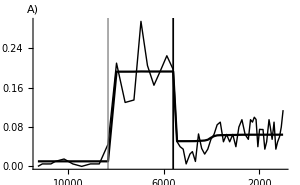

```mathematica
f1a =ListLinePlot[{e1,e2},
PlotRange-> {{1000,11500},{0,0.4}},AxesOrigin->{11500,0},
PlotStyle->{{Black,Thin},Black},AxesStyle->as,
GridLines->{{{5600,Directive[Black,AbsoluteThickness[1.25],Opacity[1]]},{8324.5,Directive[Gray,AbsoluteThickness[1.25],Opacity[0.75]]}}, None},
PlotRangePadding->None,ImageSize->is  ,ScalingFunctions->sf,
AxesLabel->aA
]
```

```mathematica
(* make sure the fitted bcp exist-need to run the R code first *)
e1 =Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_s_8_seed_5.csv"];
e2 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pm_s_8_seed_5.csv"][[2;;,;;-2]];
e3 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pp_s_8_seed_5.csv"][[2;;,;;-2]];

(* create age for the time-series *)
ne1 = {Range[11700,100,-200],e1[[10,;;;;2]]}//Transpose;
ne2 = {Range[11700,200,-200],e2[[10,;;;;2]]}//Transpose;
ne3 = {Range[11700,200,-200],e3[[10,;;;;2]]}//Transpose;
```

```mathematica
SeparateAC[{ne2[[All,1]],ne3[[All,2]],ne2[[All,2]]},0.5,True]
```

{{9089.19,-1},{6878.13,1},{729.665,-1},{514.781,-1}}

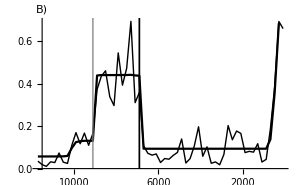

```mathematica
f1b =ListLinePlot[{ne1,ne2},
PlotRange-> {{1000,11500},{0,0.8}},AxesOrigin->{11500,0},
PlotStyle->{{Black,Thin},Black},AxesStyle->as,
GridLines->{{{9100,Directive[Gray,AbsoluteThickness[1.25],Opacity[0.75]]},{6900,Directive[Black,AbsoluteThickness[1.25],Opacity[1]]}}, None},
PlotRangePadding->None,ImageSize->is  ,ScalingFunctions->sf,
AxesLabel->aB
]
```

```mathematica
(* example of empirical data for figure 1A *)
e4 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/Fagus_1002.csv"];
e5 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/Fagus_pm_1002.csv"];
e6 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/Fagus_pp_1002.csv"];
```

```mathematica
e1//Length
```

63

```mathematica
e6
```

{{7839,0},{7763,0},{7688,0.0004},{7613,0.0002},{7575,0.0003},{7500,0.0003},{7448,0.0005},{7396,0.0667},{7344,0.9315},{7241,0.0016},{7137,0.0014},{7033,0.0008},{6929,0.001},{6826,0.0007},{6618,0},{6411,0.0001},{6022,0.0001},{5768,0.0002},{5307,0.0003},{5077,0},{4846,0.0003},{4616,0.0001},{4385,0.0001},{4176,0},{3927,0},{3802,0.0001},{3677,0},{3553,0},{3428,0},{3304,0.0001},{3223,0.0004},{3131,0.0001},{3039,0.0006},{2947,0.0005},{2854,0.0001},{2762,0.0002},{2693,0.0003},{2500,0.0001},{2330,0.0001},{2160,0.0001},{1990,0.0001},{1820,0},{1650,0.0004},{1480,0.0002},{1302,0.0007},{1195,0.0004},{1053,NA}}

```mathematica
SeparateAC[{e6[[All,1]],e6[[All,2]],e5[[All,2]]},0.5,False]
```

{{7344,-1}}

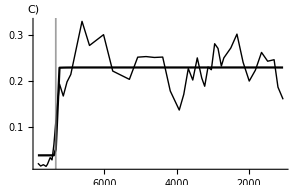

```mathematica
f1c =ListLinePlot[{e4,e5},
PlotRange-> {{1000,8000},{0,0.4}},AxesOrigin->{8000,0},
PlotStyle->{{Black,Thin},Black},AxesStyle->as,
GridLines->{{{7344,Directive[Gray,AbsoluteThickness[1.25],Opacity[0.75]]}}, None},
PlotRangePadding->None,ImageSize->is  ,ScalingFunctions->sf,
AxesLabel->aC
]
```

```mathematica
v1 =Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_s_5_seed_100.csv"];
v2 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pm_s_5_seed_100.csv"][[2;;,;;-2]];
v3 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pp_s_5_seed_100.csv"][[2;;,;;-2]];

nv1 = {Range[11700,100,-200],v1[[5,;;;;2]]}//Transpose;
nv2 = {Range[11700,200,-200],v2[[5,;;;;2]]}//Transpose;
nv3 = {Range[11700,200,-200],v3[[5,;;;;2]]}//Transpose;
```

```mathematica
SeparateAC[{nv3[[All,1]],nv3[[All,2]],nv2[[All,2]]},0.5,True]
```

{{7069.37,-1}}

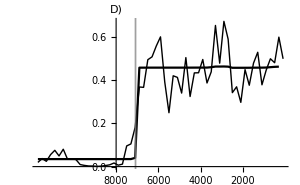

```mathematica
f1d =ListLinePlot[{nv1,nv2},
PlotRange-> {{1000,8000},{0,0.8}},AxesOrigin->{8000,0},
PlotStyle->{{Black,Thin},Black},AxesStyle->as,
GridLines->{{{7082,Directive[Gray,AbsoluteThickness[1.25],Opacity[0.75]]}}, None},
PlotRangePadding->None,ImageSize->is  ,ScalingFunctions->sf,
AxesLabel->aD
]
```

```mathematica
lg = PointLegend[{Gray,Black,Black,Gray},{"Original data","Fitted with bcp","Abrupt decrease","Abrupt increase"},LegendMarkers->{{Graphics[{Black,AbsoluteThickness[0.5],Line[{{1,0},{20,0}}]}],20},{"—",20},{"|",20},{"|",20}},LabelStyle->ls]
```

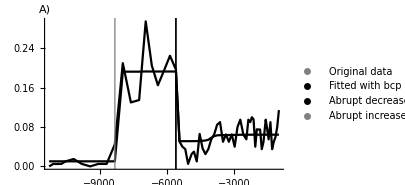
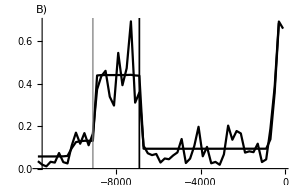
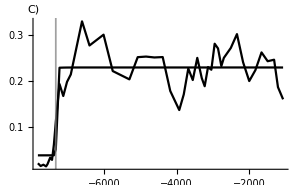
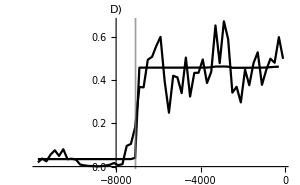
Real data | Simulated data
-Graphics- | -Graphics-
-Graphics- | -Graphics-Years Before PresentRelative abundance

```mathematica
F1 = Legended[Labeled[Grid[{{Style["Real data",FontFamily->"Arial",14],Style["Simulated data",FontFamily->"Arial",14]},{f1a,f1b },{f1c,f1d}},Spacings->{{0,1},{0,0}}],{"Years Before Present","Relative abundance"},{Bottom,Left},RotateLabel->True,LabelStyle->ls],lg]
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/latex/figs/fig1.pdf",F1]
```

/Users/gola/Box Sync/projects/ACES_paleo_lottery/latex/figs/fig1.pdf

## Figure 2

### Simulate as a function of s

```mathematica
Do[
 β = 20.; μ = 0.8; (* s =0.2;*)
SP  = {{β,μ,s},{β,μ,s},{β,μ,s}};

 TT = 1170;

out =LotteryBoundary[ TT,f =0.,σ= 0.8,Subscript[σ, l]=0.8, ρ =0.0, SP,seed = sed];

nout = out[[1,1;;-1;;10,1;;32;;4,1;;16;;4]];

dim = Dimensions[nout];
nout = Partition[Flatten[nout],dim[[2]]dim[[3]]]//Transpose;

SS =Round[s 20,1];(*Print@SS;*)

name = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_s_"<>ToString[SS]<>"_seed_"<>ToString@sed<>".csv";
Export[ name,nout];
,{s,Range[0,0.5,0.05]},{sed,100}];
```

```mathematica
Do[
 β = 20.; μ = 0.8; (* s =0.2;*)
SP  = {{β,μ,s},{β,μ,s},{β,μ,s}};

 TT = 1170;

out =LotteryBoundarySameI[TT,f =0.,σ= 0.8,Subscript[σ, l]=0.8, ρ =0.0, SP,seed = sed];

nout = out[[1,1;;-1;;10,1;;32;;4,1;;16;;4]];

dim = Dimensions[nout];
nout = Partition[Flatten[nout],dim[[2]]dim[[3]]]//Transpose;

SS =Round[s 20,1];(*Print@SS;*)

name = "/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2_same_I/sim_s_"<>ToString[SS]<>"_seed_"<>ToString@sed<>".csv";
Export[ name,nout];
,{s,Range[0,0.5,0.05]},{sed,100}];
```

### Plot examples

```mathematica
SS = {0,5,8};
SITE = 14;

sed = 6;

d1 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_s_"<>ToString[SS[[1]]]<>"_seed_"<>ToString@sed<>".csv"][[SITE]];
d2 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_s_"<>ToString[SS[[2]]]<>"_seed_"<>ToString@sed<>".csv"][[SITE]];
d3= Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_s_"<>ToString[SS[[3]]]<>"_seed_"<>ToString@sed<>".csv"][[SITE]];

d1= {Range[11700,100,-100],d1}//Transpose;
d2= {Range[11700,100,-100],d2}//Transpose;
d3= {Range[11700,100,-100],d3}//Transpose;


d1m = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pm_s_"<>ToString[SS[[1]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];
d2m = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pm_s_"<>ToString[SS[[2]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];
d3m= Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pm_s_"<>ToString[SS[[3]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];

d1m= {Range[11700,200,-100],d1m}//Transpose;
d2m= {Range[11700,200,-100],d2m}//Transpose;
d3m= {Range[11700,200,-100],d3m}//Transpose;

d1p = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pp_s_"<>ToString[SS[[1]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];
d2p = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pp_s_"<>ToString[SS[[2]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];
d3p= Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pp_s_"<>ToString[SS[[3]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];

d1p= {Range[11700,200,-100],d1p}//Transpose;
d2p= {Range[11700,200,-100],d2p}//Transpose;
d3p= {Range[11700,200,-100],d3p}//Transpose;
```

```mathematica
Select[d1p,(#[[2]]>0.5)&]
```

{}

```mathematica
ip2 = {{30,0},{20,30}};
prp = {{None,None},{5,None}};
```

```mathematica
e2a =  Text[Framed[Style["s = 0",16,FontFamily->"Arial"],Background->None,FrameMargins->Tiny],Scaled[{0.5,0.92}]];
e2b =  Text[Framed[Style["s = 0.25",16,FontFamily->"Arial"],Background->None,FrameMargins->Tiny],Scaled[{0.5,.92}]];
e2c =  Text[Framed[Style["s = 0.4",16,FontFamily->"Arial"],Background->White,FrameMargins->Tiny],Scaled[{0.5,.92}]];
```

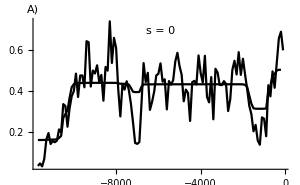
-Graphics-Years Before PresentSimulated frequency

```mathematica
f2a = Labeled[ListLinePlot[{d1,d1m},PlotRange->{{1000,11700},{0,1.}},AxesOrigin->{11700,0},PlotStyle->{{Black,Thin},Black},PlotRangePadding->None,ImageSize->is,ScalingFunctions->sf ,
Epilog-> e2a ,AxesLabel->aA,LabelStyle->ls,AxesStyle->as,ImagePadding->ip2],{"Years Before Present", "Simulated frequency"},{Bottom,Left,Top},RotateLabel->True,LabelStyle->ls]
```

```mathematica
Select[d2p,(#[[2]]>0.5)&]
```

{}

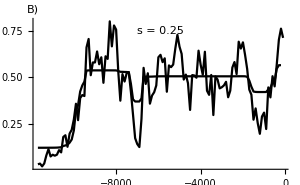
-Graphics-Years Before PresentSimulated frequency

```mathematica
f2b = Labeled[ListLinePlot[{d2,d2m},PlotRange->{{1000,11700},{0,1}},AxesOrigin->{11700,0},PlotStyle->{{Black,Thin},Black},AxesStyle->as,PlotRangePadding->None,ImageSize->is, ScalingFunctions->sf,Epilog->e2b ,LabelStyle->ls,
AxesLabel->aB,ImagePadding->ip2
],{"Years Before Present", "Simulated frequency"},{Bottom,Left,Top},RotateLabel->True,LabelStyle->ls]
```

```mathematica
Select[d3p,(#[[2]]>0.5)&]
```

{{9500,0.9937},{7300,0.8708},{6100,0.9349},{1700,0.51}}

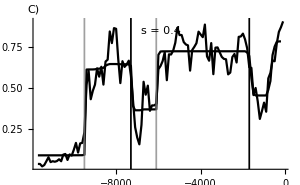
-Graphics-Years Before PresentSimulated frequency

```mathematica
f2c =Labeled[ ListLinePlot[{d3,d3m},PlotRange->{{1000,11700},{0,1}},AxesOrigin->{11700,0},PlotStyle->{{Black,Thin},Black},AxesStyle->as,PlotRangePadding->None,ImageSize->is ,ScalingFunctions->sf,ImagePadding->ip2,
GridLines->{{{9500,Directive[Gray,AbsoluteThickness[1.25],Opacity[0.75]]},{7300,Directive[Black,AbsoluteThickness[1.25],Opacity[1]]},{6100,Directive[Gray,AbsoluteThickness[1.25],Opacity[0.75]]},{1700,Directive[Black,AbsoluteThickness[1.25],Opacity[1]]}}, None},Epilog->e2c ,LabelStyle->ls,AxesLabel->aC ],{"Years Before Present", "Simulated frequency"},{Bottom,Left,Top},RotateLabel->True,LabelStyle->ls]
```

### Multi-taxa ACs

```mathematica
SP = Keys[DS]//Normal ;
```

```mathematica
dd1 = Table[nm-> {(DA[All,nm<>"_AI"]//Total)  ,(DA[All,nm<>"_AD"]//Total) }, {nm,SP}]//Association
```

<|Alnus→{1,0},Fagus→{15,2},Juglans→{0,2},Picea→{8,7},PinusPinus→{2,4},PinusStrobus→{4,3},Platanus→{0,1},Tilia→{0,1},Tsuga→{14,14},Ulmus→{5,15}|>

```mathematica
posi = AssociationThread[SP,{After,Before,After,After,Before,After,After,Below,Before,Before}];
```

```mathematica
(*the +1 is to avoid zero in the log plot *)dd1=Table[Callout[{1+ (DA[All,nm<>"_AI"]//Total),1+ (DA[All,nm<>"_AD"]//Total)},Style[nm,"Italic"],CalloutMarker-> "CirclePoint",LabelStyle->Directive[12,Black,FontFamily->"Helvetica"],Appearance->"CurvedLeader"],{nm,SP}]
```

{Callout[{2,1},Alnus,CalloutMarker→CirclePoint,LabelStyle→Directive[12,GrayLevel[0],FontFamily→Helvetica],Appearance→CurvedLeader],Callout[{16,3},Fagus,CalloutMarker→CirclePoint,LabelStyle→Directive[12,GrayLevel[0],FontFamily→Helvetica],Appearance→CurvedLeader],Callout[{1,3},Juglans,CalloutMarker→CirclePoint,LabelStyle→Directive[12,GrayLevel[0],FontFamily→Helvetica],Appearance→CurvedLeader],Callout[{9,8},Picea,CalloutMarker→CirclePoint,LabelStyle→Directive[12,GrayLevel[0],FontFamily→Helvetica],Appearance→CurvedLeader],Callout[{3,5},PinusPinus,CalloutMarker→CirclePoint,LabelStyle→Directive[12,GrayLevel[0],FontFamily→Helvetica],Appearance→CurvedLeader],Callout[{5,4},PinusStrobus,CalloutMarker→CirclePoint,LabelStyle→Directive[12,GrayLevel[0],FontFamily→Helvetica],Appearance→CurvedLeader],Callout[{1,2},Platanus,CalloutMarker→CirclePoint,LabelStyle→Directive[12,GrayLevel[0],FontFamily→Helvetica],Appearance→CurvedLeader],Callout[{1,2},Tilia,CalloutMarker→CirclePoint,LabelStyle→Directive[12,GrayLevel[0],FontFamily→Helvetica],Appearance→CurvedLeader],Callout[{15,15},Tsuga,CalloutMarker→CirclePoint,LabelStyle→Directive[12,GrayLevel[0],FontFamily→Helvetica],Appearance→CurvedLeader],Callout[{6,16},Ulmus,CalloutMarker→CirclePoint,LabelStyle→Directive[12,GrayLevel[0],FontFamily→Helvetica],Appearance→CurvedLeader]}

```mathematica
(* this has to be done manually because of the names of Pinus are spaced and the position of the callout is manually inserted*)dd1 = {Callout[{2,1},Style["Alnus",Italic],After,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],
Callout[{16,3},Style["Fagus",Italic],Before,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],
Callout[{1,3},Style["Juglans",Italic],After,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],
Callout[{9,8},Style["Picea",Italic],After,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],
Callout[{3,5},Style["Pinus Pinus",Italic],Before,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],
Callout[{5,4},Style["Pinus Strobus",Italic],After,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],
Callout[{1,2},Style["Platanus",Italic],After,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],
Callout[{1,2},Style["Tilia",Italic],Below,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],
Callout[{15,15},Style["Tsuga",Italic],Before,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],
Callout[{6,16},Style["Ulmus",Italic],Before,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"]};
```

```mathematica
dd1x = Table[{i,i},{i,1,20,1}];
```

```mathematica
tx2 = {{1,0},{2,1},{3,2},{5,4},{9,8},{17,16}};
```

```mathematica
f2d =Labeled[ ListLogLogPlot[{dd1,dd1x},Joined->{False,True}, PlotStyle->{Automatic, Directive[Gray,AbsoluteThickness[1]]},ImageSize->is,LabelStyle->ls,PlotRange->{{0.8,22},{0.8,22}},PlotRangePadding->None,AxesLabel->aD,AxesStyle->as,ImagePadding->ip2,Ticks->{tx2,tx2}]
,{"Total number of abrupt increases","Total number of \nabrupt decreases"},{Bottom,Left},RotateLabel->True,LabelStyle->ls]
```

-Graphics-Total number of abrupt increasesTotal number of 
abrupt decreases

### Plotting theoretical results

```mathematica
(* runs a code assuming same initial conditions *)
STT= SII = SDD = {};
Do[
TT = II = DD = {};
Do[
dp = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2_same_I/sim_pp_s_"<>ToString@s<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]];
dm = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2_same_I/sim_pm_s_"<>ToString@s<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]];

lt = Length[dp[[1]]];
tt = Range[lt];
ll = Length[dp];
ACT = ACI  = ACD = {};
 Do[
tp = dp[[i]];
tm = dm[[i]];

ac = SeparateAC[{tt,tp,tm}][[All,2]];
act = Length[ac];
aci = Count[ac,-1];
acd = Count[ac,1];
AppendTo[ACT, act];
AppendTo[ACI, aci];
AppendTo[ACD, acd];
,{i,ll}];

AppendTo[TT, ACT];
AppendTo[II, ACI];
AppendTo[DD, ACD];
,{s,0,10,1}];

AppendTo[STT, TT];
AppendTo[SII,II];
AppendTo[SDD, DD];

,{sed,100}];
```

```mathematica
SII2 = SII;
SDD2 = SDD;
STT2 = STT;
```

```mathematica
xx =Range[0,0.5,0.05];
mi2 = Table[SII2[[rep,s]]//Mean//N,{s,Length@xx},{rep,10}];
md2 = Table[SDD2[[rep,s]]//Mean//N,{s,Length@xx},{rep,10}];
msd2 = Table[STT2[[rep,s]]//StandardDeviation//N,{s,Length@xx},{rep,10}];
```

```mathematica
(* for abrupt increases *)
MI2 = {xx,Map[Mean,mi2]}//Transpose;
MIAX2 ={xx,Map[Max,mi2]}//Transpose;
MIIN2 ={xx,Map[Min,mi2]}//Transpose;

(* for all abrupt decreases *)
MD2 = {xx,Map[Mean,md2]}//Transpose;
MDAX2 ={xx,Map[Max,md2]}//Transpose;
MDIN2 ={xx,Map[Min,md2]}//Transpose;
```

```mathematica
pr = {All,{0,3}};
ii2 = ListLinePlot[{MI2},PlotRange->pr,PlotStyle->Directive[Gray](*,Filling->{2->{3}},FillingStyle->{LightRed,LightRed}*),PlotRangePadding->None];
dd2= ListLinePlot[{MD2},PlotRange->pr,PlotStyle->Directive[Black](*,Filling->{2->{3}},FillingStyle->{LightBlue,LightBlue}*),PlotRangePadding->None];
```

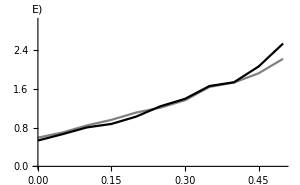
-Graphics-Strength of frequency dependence (s)Average number of 
abrupt changes

```mathematica
f2e = Labeled[Show[ii2,dd2,LabelStyle->ls,ImageSize->is,AxesLabel->aE,ImagePadding->ip2,AxesStyle->as],{"Strength of frequency dependence (s)", "Average number of \nabrupt changes"},{Bottom,Left},RotateLabel->True,LabelStyle->ls]
```

```mathematica
STT= SII = SDD = {};
Do[ (* for each seed *)
TT = II = DD = {};
Do[ (* for each value of s *)
dp = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pp_s_"<>ToString@s<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]];
dm = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig2/sim_pm_s_"<>ToString@s<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]];

lt = Length[dp[[1]]];
tt = Range[lt];
ll = Length[dp];
ACT = ACI  = ACD = {};
 Do[ (*for each site *)
tp = dp[[i]];
tm = dm[[i]];

ac = SeparateAC[{tt,tp,tm}][[All,2]];
act = Length[ac];
aci = Count[ac,-1];
acd = Count[ac,1];
AppendTo[ACT, act];
AppendTo[ACI, aci];
AppendTo[ACD, acd];
,{i,ll}];

AppendTo[TT, ACT];
AppendTo[II, ACI];
AppendTo[DD, ACD];
,{s,0,10,1}];

AppendTo[STT, TT];
AppendTo[SII,II];
AppendTo[SDD, DD];

,{sed,100}];
```

```mathematica
(* xx is for x coordinate for plotting *)
xx =Range[0,0.5,0.05];
mi = Table[SII[[rep,s]]//Mean//N,{s,Length@xx},{rep,100}];
md = Table[SDD[[rep,s]]//Mean//N,{s,Length@xx},{rep,100}];
msd = Table[STT[[rep,s]]//StandardDeviation//N,{s,Length@xx},{rep,100}];
```

```mathematica
(* for all abrupt increases *)
MI = {xx,Map[Mean,mi]}//Transpose;
(* if min-max envelop is needed;
MIAX ={xx,Map[Max,mi]}//Transpose;
MIIN ={xx,Map[Min,mi]}//Transpose;
*)
(* for all abrupt decreases *)
MD = {xx,Map[Mean,md]}//Transpose;
(* if min-ma envelop is needed;
MDAX ={xx,Map[Max,md]}//Transpose;
MDIN ={xx,Map[Min,md]}//Transpose;
*)
```

```mathematica
Map[Mean,mi]/Map[Mean,md]
```

{1.68307,1.6465,1.57272,1.51541,1.46214,1.47118,1.44353,1.45382,1.45013,1.40328,1.22591}

```mathematica
pr = {All,{0,3}};
ii = ListLinePlot[{MI},PlotRange->pr,PlotStyle->{Gray,LightRed,LightRed}(*,Filling->{2->{3}},FillingStyle->{LightRed,LightRed}*),PlotRangePadding->None];
dd = ListLinePlot[{MD},PlotRange->pr,PlotStyle->{Black,LightBlue,LightBlue}(*,Filling->{2->{3}},FillingStyle->{LightBlue,LightBlue}*),PlotRangePadding->None];
```

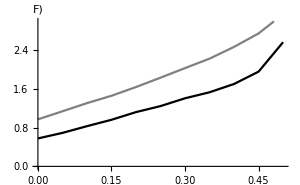
-Graphics-Strength of frequency-dependence (s)Average number of 
abrupt changes

```mathematica
f2f = Labeled[Show[ii,dd,(*ii2,dd2,*)LabelStyle->ls,ImageSize->is,AxesLabel->aF,ImagePadding->ip2,AxesStyle->as],{"Strength of frequency-dependence (s)", "Average number of \nabrupt changes"},{Bottom,Left},RotateLabel->True,LabelStyle->ls]
```

```mathematica
lg2 = LineLegend[{Black, Gray},Style[#, 16,FontFamily->"Arial"]&/@{"Abrupt decreases", "Abrupt increases"}]
```

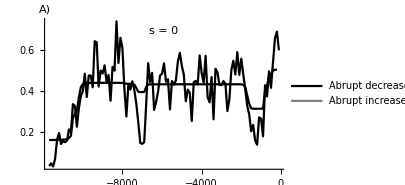
-Graphics-Years Before PresentSimulated frequency | -Graphics-Total number of abrupt increasesTotal number of 
abrupt decreases
-Graphics-Years Before PresentSimulated frequency | -Graphics-Strength of frequency dependence (s)Average number of 
abrupt changes
-Graphics-Years Before PresentSimulated frequency | -Graphics-Strength of frequency-dependence (s)Average number of 
abrupt changes

```mathematica
F2 = Legended[Grid[{{f2a, f2b,f2c}, {f2d,f2e,f2f}}//Transpose,Spacings-> {2,1}],lg2]
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/latex/figs/fig2.pdf",F2]
```

/Users/gola/Box Sync/projects/ACES_paleo_lottery/latex/figs/fig2.pdf

## Figure 3

```mathematica
ip3a = {{0,2},{8,6}};
ip3 = {{24,0},{20,30}};gr ={{37.,56.},{-105.,-59.}};tx = {Automatic,{{0,"0.0"},{0.0005,"0.5"},{0.001,"1.0"},{0.0015,"1.5"},{0.003,"2.0"}}};
```

```mathematica
pt3a =  {Graphics[Inset[Style["×",16,Orange]],ImageSize->15], Graphics[{EdgeForm[{AbsoluteThickness[0.5], White}],FaceForm[ Black],Disk[{0,0},0.1]}]};
SeedRandom[1];
allpx = DeleteCases[Table[If[ DA[i,"num_AD"]==0,{GeoMarker[ Values[Normal[DA[i,{"lat","lon"}]]],pt3a[[1]],"Scale"-> 2]}],{i,Length@DA}],Null];
allpo = DeleteCases[Table[If[DA[i,"num_AD"]≠ 0,{GeoMarker[ Values[Normal[DA[i,{"lat","lon"}]]],pt3a[[2]],"Scale"-> 2]}],{i,Length@DA}],Null];
allp = Join[allpo,allpx];

f3a=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,PlotLabel->"A)                                                                     ",LabelStyle->Directive[Black,12,FontFamily->"Arial"],ImagePadding->ip3a] ;
```

```mathematica
Length@allpcx
```

```mathematica
Length@allpx
```

36

```mathematica
pt3c =  {Graphics[Inset[Style["×",16,Orange]],ImageSize->15], Graphics[{EdgeForm[{AbsoluteThickness[0.5], White}],FaceForm[ Gray],Disk[{0,0},0.1]}]};
SeedRandom[1];
allpcx = DeleteCases[Table[If[ DA[i,"num_AI"]== 0,{GeoMarker[ Values[Normal[DA[i,{"lat","lon"}]]],pt3c[[1]],"Scale"-> 2]}],{i,Length@DA}],Null];
allpco = DeleteCases[Table[If[DA[i,"num_AI"]≠ 0,{GeoMarker[ Values[Normal[DA[i,{"lat","lon"}]]],pt3c[[2]],"Scale"-> 2]}],{i,Length@DA}],Null];
allpc = Join[allpco,allpcx];

f3c=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allpc},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allpc}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,PlotLabel->"C)                                                                     ",LabelStyle->Directive[Black,12,FontFamily->"Arial"] ,ImagePadding->ip3a] ;
```

```mathematica
allAD = Table[DS[nm,All,"AD"]//DeleteMissing//Normal //Values ,{nm,SP}]//Flatten;
allAI = Table[DS[nm,All,"AI"]//DeleteMissing//Normal //Values ,{nm,SP}]//Flatten;
```

```mathematica
diffAD= Differences[Sort[allAD]];
cvAD =Round[ StandardDeviation[diffAD]/Mean[diffAD]//N,0.01];
egAD =  Text[Framed[Style["N = "<> ToString@Length@allAD <> "\n CV = " <> ToString@cvAD,12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.88}]];
gAD  = {allAD,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[allAD]]}//Transpose;

diffAI= Differences[Sort[allAI]];
cvAI =Round[ StandardDeviation[diffAI]/Mean[diffAI]//N,0.01];
egAI =  Text[Framed[Style["N = "<> ToString@Length@allAI <> "\n CV = " <> ToString@cvAI,12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.88}]];
gAI  = {allAI,ConstantArray[Directive[Gray,AbsoluteThickness[1],Opacity[1]],Length[allAI]]}//Transpose;
```

```mathematica
f3b=Labeled[ SmoothHistogram[allAD,{200,"Gaussian"},
Epilog->egAD,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gAD,None},LabelStyle->ls,ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip3,AxesLabel->aB],{"Density","Years Before Present"},{Left,Bottom},RotateLabel->True,LabelStyle->ls];
f3d = Labeled[SmoothHistogram[allAI,{200,"Gaussian"},
Epilog->egAI,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gAI,None},LabelStyle->ls,ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip3,AxesLabel->aD],{"Density","Years Before Present"},{Left,Bottom},RotateLabel->True,LabelStyle->ls];
```

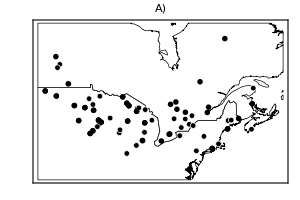
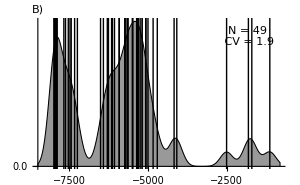
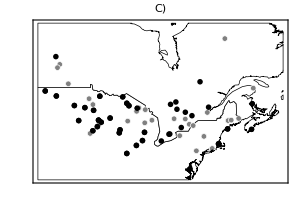
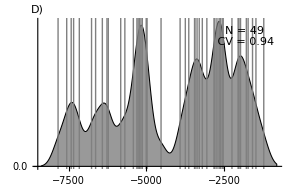
Abrupt decreases | 
-Graphics- | -Graphics-DensityYears Before Present
Abrupt increases | 
-Graphics- | -Graphics-DensityYears Before Present

```mathematica
F3 = Grid[{{Style["Abrupt decreases",18, FontFamily->"Arial"],SpanFromLeft},{f3a,f3b},{Style["Abrupt increases",18, FontFamily->"Arial"],SpanFromLeft},{f3c,f3d}},Spacings->{Automatic,{0,0,1}}]
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/latex/figs/fig3.pdf",F3];
```

### Recycle if there is an need to partition the abrupt changes between 2 groups of species

```mathematica
SPd = DeleteCases[SP, "Tsuga"|"Fagus"|"Picea"];
SPi = DeleteCases[SP, "Tsuga"|"Ulmus"|"Picea"];
SPD = Complement[SP,SPD];
SPI = Complement[SP,SPI];
```

```mathematica
allAD = Table[DS[nm,All,"AD"]//DeleteMissing//Normal //Values ,{nm,SPD}]//Flatten;
allAI = Table[DS[nm,All,"AI"]//DeleteMissing//Normal //Values ,{nm,SPI}]//Flatten;
```

```mathematica
diffAI= Differences[Sort[allAI]];
cvAI =Round[ StandardDeviation[diffAI]/Mean[diffAI]//N,0.01];
egAI =  Text[Framed[Style["N = "<> ToString@Length@allAI <> "\n CV = " <> ToString@cvAI,12,FontFamily->"Helevetica"],Background->White],Scaled[{0.85,.88}]];
gAI  = {allAI,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[allAI]]}//Transpose;

diffAD= Differences[Sort[allAD]];
cvAD =Round[ StandardDeviation[diffAD]/Mean[diffAD]//N,0.01];
egAD =  Text[Framed[Style["N = "<> ToString@Length@allAD <> "\n CV = " <> ToString@cvAD,12,FontFamily->"Helevetica"],Background->White],Scaled[{0.85,.88}]];
gAD  = {allAD,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[allAD]]}//Transpose;
```

```mathematica
tx = {Automatic,{{0,"0.0"},{0.0005,"0.5"},{0.001,"1.0"},{0.0015,"1.5"},{0.003,"2.0"}}};
```

```mathematica
f2a = SmoothHistogram[allAI,{200,"Gaussian"},
Epilog->egAI,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gAI,None},LabelStyle->ls,PlotLabel-> "Abrupt increases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2];
f2b = SmoothHistogram[allAD,{200,"Gaussian"},
Epilog->egAD,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gAD,None},LabelStyle->ls,PlotLabel-> "Abrupt decreases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2];
```

```mathematica
allad = Table[DS[nm,All,"AD"]//DeleteMissing//Normal //Values ,{nm,SPd}]//Flatten;
allai = Table[DS[nm,All,"AI"]//DeleteMissing//Normal //Values ,{nm,SPi}]//Flatten;
```

```mathematica
diffai= Differences[Sort[allai]];
cvai =Round[ StandardDeviation[diffai]/Mean[diffai]//N,0.01];
egai =  Text[Framed[Style["N = "<> ToString@Length@allai <> "\n CV = " <> ToString@cvai,12,FontFamily->"Helevetica"],Background->White],Scaled[{0.85,.88}]];
gai  = {allai,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[allai]]}//Transpose;

diffad= Differences[Sort[allad]];
cvad =Round[ StandardDeviation[diffad]/Mean[diffad]//N,0.01];
egad =  Text[Framed[Style["N = "<> ToString@Length@allad <> "\n CV = " <> ToString@cvad,12,FontFamily->"Helevetica"],Background->White],Scaled[{0.85,.88}]];
gad  = {allad,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[allad]]}//Transpose;
```

```mathematica
f3a = SmoothHistogram[allai,{200,"Gaussian"},
Epilog->egai,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gai,None},LabelStyle->ls,PlotLabel-> "Abrupt increases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2];
f3b = SmoothHistogram[allad,{200,"Gaussian"},
Epilog->egad,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gad,None},LabelStyle->ls,PlotLabel-> "Abrupt decreases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2];
```

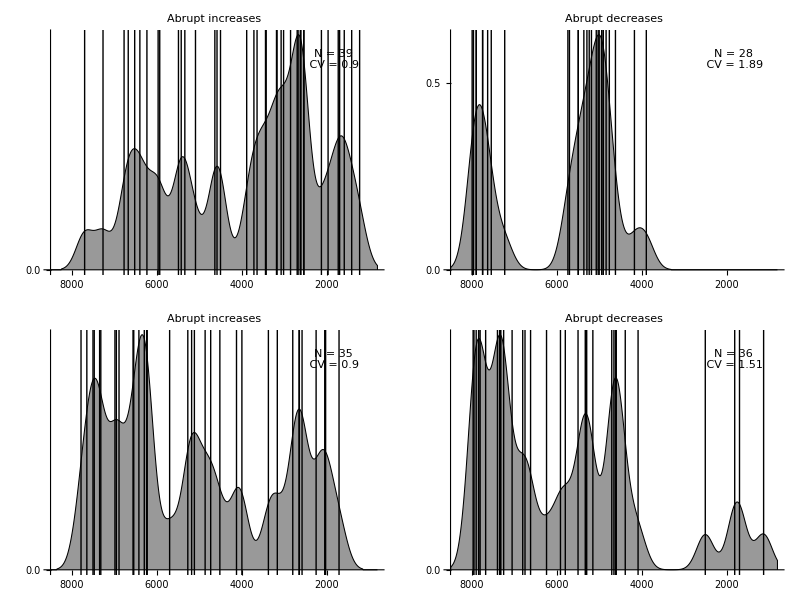

```mathematica
d2 =Grid[{{f2a,f2b},{f3a,f3b}}]
```

## Figure 4

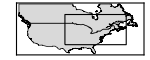

```mathematica
(*(* uncomment if an inset needs to be created *)f3inset =GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[LightGray]],Polygon[ LinguisticAssistant]},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[LightGray]],Polygon[ LinguisticAssistant]},EdgeForm[{Thick,Black}],FaceForm[],Rectangle[{-100,35},{-60,65}]}, GeoRange->{{25,60},{-130,-50}},ImageSize->150,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White], AspectRatio->1/2.5,GeoProjection->"Mercator"]
*)
```

```mathematica
(* get latitude and longitude coordinates*)
site = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/hemlock_data/dataset_info.csv"][[2;;,{3,5,6}]];
 SAC  ={};
Do[(* for each site *)
id = finalID[[i]];
pos = Position[site[[All,1]],id][[1,1]];
coord = site[[pos,{2,3}]];
dm  =Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/hemlock_data/tsuga_pm_"<>ToString@id<>".csv"][[2;;-2]];
dp = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/hemlock_data/tsuga_pp_"<>ToString@id<>".csv"][[2;;-2]];

temp = SeparateAC[{dp[[All,1]],dp[[All,2]],dm[[All,2]]},0.5, False];
ll = Length[temp];
sac = Partition[{temp,ConstantArray[coord, ll]}//Transpose//Flatten,4];

AppendTo[SAC,sac];
,{i,Length@finalID}];
```

```mathematica
(* separates the abrupt increase and decrease from the empirical data *)
DAT = Partition[SAC//Flatten,4];
empi = Select[DAT,(#[[2]]==-1 &)];
empd= Select[DAT,(#[[2]]==1 &)];
```

```mathematica
empi//Length
```

40

```mathematica
empd//Length
```

23

```mathematica
40/23.
```

1.73913

```mathematica
SeedRandom[1]; (* fix random seed so that the location of the dots are 'reproducible' *)
nD = Table[{GeoMarker[RandomReal[{-0.25,0.25},2] + empd[[i,{3,4}]],StyleSelector[empd[[i,1]]],"Scale"-> 1.0]},{i,Length@empd}];
nI = Table[{GeoMarker[RandomReal[{-0.25,0.25},2] + empi[[i,{3,4}]],StyleSelector[empi[[i,1]]],"Scale"-> 1.0]},{i,Length@empi}];
```

```mathematica
gr ={{37.,50.},{-90.,-60.}};
lg4 = BarLegend[GrayLevel,{0.2,0.5,0.9,0.91},"Ticks"-> {0, 0.3,0.4,0.8,1},"TickLabels" -> st,LegendMarkerSize->200,LegendLabel-> Style["YBP  ",16,FontFamily->"Arial"] ]
```

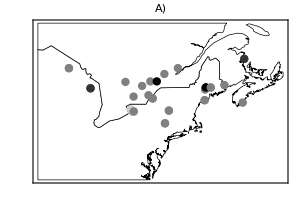

```mathematica
f4A=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],nD},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],nD}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,PlotLabel->"A)                                                                     ",LabelStyle->Directive[Black,12,FontFamily->"Arial"] ]
```

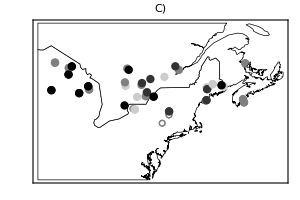

```mathematica
f4C=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],nI},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],nI}}, 
GeoProjection-> "Mercator",GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,PlotLabel->"C)                                                                     ",LabelStyle->Directive[Black,12,FontFamily->"Arial"]]
```

```mathematica
(* import an illustrative example*)

RR = 5; sed=1;
name = "/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig5a/sim_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
dat = Import[name];

namep = "/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig5a/sim_pp_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
namem = "/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig5a/sim_pm_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
dp = Import[namep][[2;;,;;-2]];
dm = Import[namem][[2;;,;;-2]];
```

```mathematica
SAC1  ={};
RandomSeed[1];
XX = Range[11700,200,-100];
Do[(* for each site *)

coord = XY[[i]];
temp = SeparateAC[{XX+ RandomReal[{-50,50},Length@XX],dp[[i]],dm[[i]]},0.5, False];
ll = Length[temp];
sac = Partition[{temp,ConstantArray[coord, ll]}//Transpose//Flatten,4];

AppendTo[SAC1,sac];
,{i,32}];
```

```mathematica
(* separates the abrupt increase and decrease from the simulated data *)
DAT1 = Partition[SAC1//Flatten,4];
simd1 =Select[DAT1,#[[2]] == 1 &][[All,{1,3,4}]]//Sort;
simi1  = Select[DAT1,#[[2]] == -1 &][[All,{1,3,4}]]//Sort;
```

```mathematica
SeedRandom[1];
nD1 = Table[{GeoMarker[RandomReal[{-0.75,0.75},2] + simd1[[i,{2,3}]],StyleSelector[simd1[[i,1]]],"Scale"-> 1.0]},{i,Length@simd1}];
nI1 = Table[{GeoMarker[RandomReal[{-0.75,0.75},2] + simi1[[i,{2,3}]],StyleSelector[simi1[[i,1]]],"Scale"-> 1.0]},{i,Length@simi1}];
```

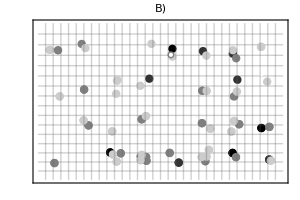

```mathematica
f4B=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],White]],FaceForm[White]],Polygon[ LinguisticAssistant],nD1},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],White]],FaceForm[White]],Polygon[ LinguisticAssistant],nD1}},GeoGridLines->{Subdivide[37,50,16],Subdivide[-90.,-60.,32]},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,PlotLabel->"B)                                                                     ",LabelStyle->Directive[Black,12,FontFamily->"Arial"]]
```

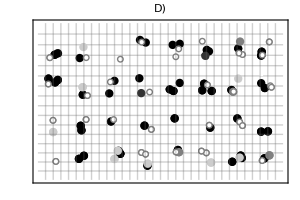

```mathematica
f4D=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],White]],FaceForm[White]],Polygon[ LinguisticAssistant],nI1},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],White]],FaceForm[White]],Polygon[ LinguisticAssistant],nI1}},GeoGridLines->{Subdivide[37,50,16],Subdivide[-90.,-60.,32]},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,PlotLabel->"D)                                                                     ",LabelStyle->Directive[Black,12,FontFamily->"Arial"]]
```

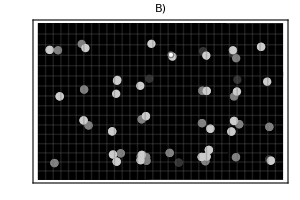
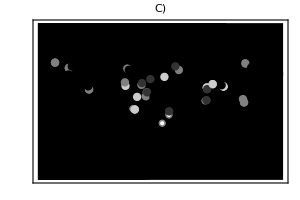
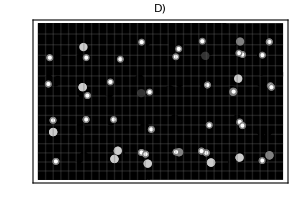
| T. canadensis data | Simulated data
Abrupt decreases     | -Graphics- | -Graphics-
Abrupt increases     | -Graphics- | -Graphics-

```mathematica
F4 =  Legended[Grid[{{"",Row[{Style["T. canadensis ",Italic,18, FontFamily->"Arial"],Style["data",18, FontFamily->"Arial"]}], Style["Simulated data",18, FontFamily->"Arial"]},{Rotate[Style["Abrupt decreases    ",18, FontFamily->"Arial"],Pi/2],f4A,f4B},{Rotate[Style["Abrupt increases    ",18, FontFamily->"Arial"],Pi/2],f4C,f4D}}],lg4]
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/latex/figs/fig4.pdf",F4]
```

/Users/gola/Box Sync/projects/ACES_paleo_lottery/latex/figs/fig4.pdf

## Figure 5

```mathematica
(* manually selected ticks for the y-axis*)
tx = {Automatic,{{0,"0.0"},{0.0005,"0.5"},{0.001,"1.0"}}};
```

```mathematica
(* import empirical data *)
DA = SAC  ={};
Do[ (* for each site *)

da = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/hemlock_data/tsuga_"<>ToString@id<>".csv"][[2;;-2]];
dm  =Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/hemlock_data/tsuga_pm_"<>ToString@id<>".csv"][[2;;-2]];
dp = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/hemlock_data/tsuga_pp_"<>ToString@id<>".csv"][[2;;-2]];

dp = {dp[[All,1]],Unitize[dp[[All,2]],0.5]}//Transpose;
sac = SeparateAC[{dp[[All,1]],dp[[All,2]],dm[[All,2]]},0.5, False];

AppendTo[DA,da];
AppendTo[SAC,sac];
,{id,finalID}];
```

```mathematica
pr3a = {{1200,10500},{0,0.6}};
pr3aa= {{1200,10500},{0,1.0}};
pr3b =  {{1200,10500},{0,0.001}};
```

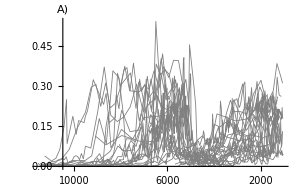

```mathematica
f5A=ListLinePlot[DA,PlotRange->pr3a,AxesOrigin->{10500,0},PlotStyle->Directive[Gray,AbsoluteThickness[0.6]],AxesStyle->as,PlotRangePadding->None,ImageSize->is ,ScalingFunctions->sf,LabelStyle->ls ,AxesLabel->aA]
```

```mathematica
(* separates the abrupt increase and decrease from the empirical data *)
dat =Partition[SAC//Flatten,2]//Sort;
empi = Select[dat,(#[[2]]==-1 &)][[All,1]];
empd = Select[dat,(#[[2]]==1 &)][[All,1]];

g1  = {empd,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[empd]]}//Transpose;
g2  = {empi,ConstantArray[Directive[Gray,AbsoluteThickness[1],Opacity[1]],Length[empi]]}//Transpose;
```

```mathematica
(* compute the coefficient of variation *)
edi = Differences[empi] ;
edd = Differences[empd] ;
cvi1 = StandardDeviation@edi/Mean@edi; 
cvd1 = StandardDeviation@edd/Mean@edd;
```

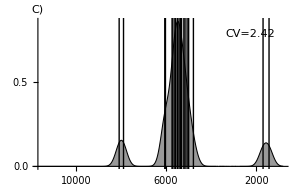

```mathematica
f5C= SmoothHistogram[empd,{200,"Gaussian"},
Epilog->Text[Framed[Style["CV="<>ToString@Round[cvd1,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g1,None},LabelStyle->ls,AxesLabel->aC,ImageSize->is,Ticks->tx,PlotRangeClipping->False]
```

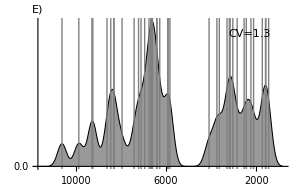

```mathematica
f5E = SmoothHistogram[empi,{200,"Gaussian"},
Epilog->Text[Framed[Style["CV="<>ToString@Round[cvi1,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g2,None},LabelStyle->ls,AxesLabel->aE,ImageSize->is,Ticks->tx,PlotRangeClipping->False]
```

```mathematica
(* import a good looking simulated data, one needs to run codes for figure 5 first *)
RR =5; sed = 1;name = "/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig5a/sim_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
dat2 = Import[name];

namep = "/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig5a/sim_pp_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
namem = "/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/simulated_data/fig5a/sim_pm_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
dp2 = Import[namep][[2;;,;;-2]];
dm2 = Import[namem][[2;;,;;-2]];
```

```mathematica
(* select some good looking sites *)
sID = {1,4,5,6,7,9,10,11,12,14,15,18,19,23,24,27,29,31,32};
simDA2 = Table[{Range[11700,100,-100] +RandomReal[{-50,50},117],dat2[[i]]}//Transpose,{i,sID}];
```

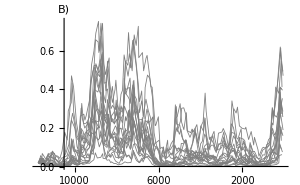

```mathematica
f5B= ListLinePlot[simDA2,PlotRange->pr3aa,AxesOrigin->{10500,0},PlotStyle->Directive[Gray,AbsoluteThickness[0.6]],AxesStyle->as,PlotRangePadding->None,ImageSize->is ,ScalingFunctions->sf,LabelStyle->ls ,AxesLabel->aB]
```

```mathematica
SeedRandom[1];
xx = Range[11700,100,-100];
SAC2= {};
Do[
 sac2 = SeparateAC[{xx + RandomReal[{-50,50},Length@xx],dp2[[i]],dm2[[i]]},0.5, False];
AppendTo[SAC2,sac2];

,{i, sID}];

(* separates the abrupt increase and decrease from the empirical data *)
sim2 =Partition[SAC2//Flatten,2]//Sort;
simi2 = Select[sim2,(#[[2]]==-1 &)][[All,1]];
simd2 = Select[sim2,(#[[2]]==1 &)][[All,1]];

g5  = {simd2,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[simd2]]}//Transpose;
g6 = {simi2,ConstantArray[Directive[Gray,AbsoluteThickness[1],Opacity[1]],Length[simi2]]}//Transpose;
```

```mathematica
sdi2 = Differences[simi2] ;
sdd2 = Differences[simd2] ;
cvi3 = StandardDeviation@sdi2/Mean@sdi2; 
cvd3 = StandardDeviation@sdd2/Mean@sdd2;
```

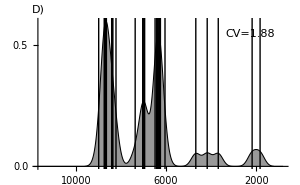

```mathematica
f5D= SmoothHistogram[simd2,{200,"Gaussian"},Epilog->Text[Framed[Style["CV="<>ToString@Round[cvd3,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle-> as, PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g5,None},LabelStyle->ls,ImageSize->is ,AxesLabel->aD,Ticks->tx]
```

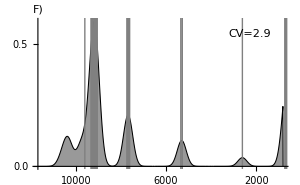

```mathematica
f5F= SmoothHistogram[simi2,{200,"Gaussian"},
Epilog->Text[Framed[Style["CV="<>ToString@Round[cvi3,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle-> as, PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g6,None},LabelStyle->ls, ImageSize->is ,AxesLabel->aF,Ticks->tx]
```

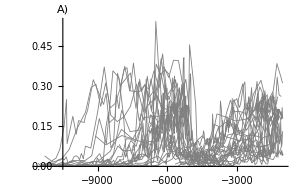
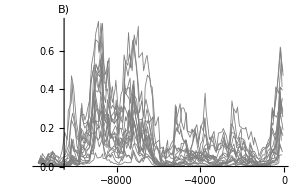
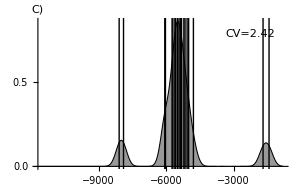
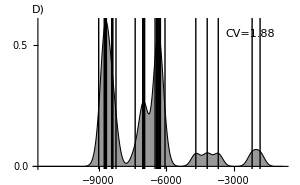
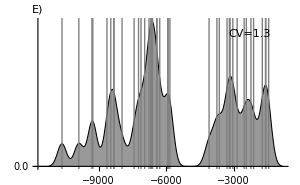
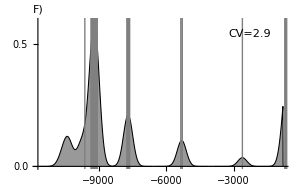
| T. canadensis data | Simulated data (ρ = 0.5) | 
Relative abundance | -Graphics- | -Graphics- | 
Density | -Graphics- | -Graphics- | Abrupt decreases
Density | -Graphics- | -Graphics- | Abrupt increasesYears Before Present

```mathematica
F5 =Labeled[Grid[{{"",Row[{Style["T. canadensis",Italic,16,FontFamily->"Arial"],Style[" data",16,FontFamily->"Arial"]}],Style["Simulated data (ρ = 0.5)",16,FontFamily->"Arial"],""},{Rotate[Style["Relative abundance",16,FontFamily->"Arial"],Pi/2],f5A,f5B,""},{Rotate[Style["Density",16,FontFamily->"Arial"],Pi/2],f5C,f5D,Rotate[Style["Abrupt decreases",16,FontFamily->"Arial"],Pi/2]},{Rotate[Style["Density",16,FontFamily->"Arial"],Pi/2],f5E,f5F,Rotate[Style["Abrupt increases",16,FontFamily->"Arial"],Pi/2]}}],"Years Before Present",Bottom,LabelStyle->ls]
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/latex/figs/fig5.pdf",F5]
```

/Users/gola/Box Sync/projects/ACES_paleo_lottery/latex/figs/fig5.pdf

#### recycle rho = 0, if one needs to show an intermediate scenario with the simulated data where rho = 0.

```mathematica
RR =0; sed = 1;name = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>"_s_0.2.csv";
dat1 = Import[name];

namep = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_pp_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>"_s_0.2.csv";
namem = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_pm_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>"_s_0.2.csv";
dp1 = Import[namep][[2;;,;;-2]];
dm1 = Import[namem][[2;;,;;-2]];
```

```mathematica
simDA1 = Table[{Range[11500,100,-100] +RandomReal[{-50,50},115],dat1[[i]]}//Transpose,{i,1,Length@dat1,2}];
```

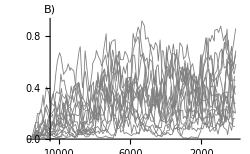

```mathematica
f4B= ListLinePlot[simDA1,PlotRange->pr3aa,AxesOrigin->{10500,0},PlotStyle->Directive[Gray,AbsoluteThickness[0.6]],AxesStyle->as,PlotRangePadding->None,ImageSize->is ,ScalingFunctions->sf,LabelStyle->ls ,AxesLabel->aB]
```

```mathematica
RandomSeed[1];
xx = Range[11500,200,-100];
SAC1= {};
Do[
 sac = SeparateAC[{xx + RandomReal[{-50,50},Length@xx],dp1[[i]],dm1[[i]]},0.5, False];
AppendTo[SAC1,sac];

,{i, 1,Length@dat,2}];

sim1 =Partition[SACx//Flatten,2]//Sort;
simi1 = Select[sim1,(#[[2]]==-1 &)][[All,1]];
simd1 = Select[sim1,(#[[2]]==1 &)][[All,1]];

g3  = {simd1,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[simd1]]}//Transpose;
g4 = {simi1,ConstantArray[Directive[Gray,AbsoluteThickness[1],Opacity[1]],Length[simi1]]}//Transpose;
```

```mathematica
sdi1 = Differences[simi1] ;
sdd1 = Differences[simd1] ;
cvi2 = StandardDeviation@sdi1/Mean@sdi1; 
cvd2 = StandardDeviation@sdd1/Mean@sdd1;
```

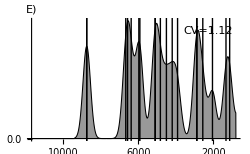

```mathematica
f4E= SmoothHistogram[simd1,{200,"Gaussian"},
Epilog->Text[Framed[Style["CV="<>ToString@Round[cvd2,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle-> as, PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g3,None},LabelStyle->ls,ImageSize->is ,AxesLabel->aE,Ticks->tx]
```

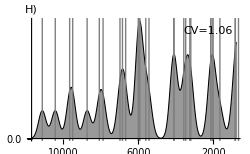

```mathematica
f4H= SmoothHistogram[simi1,{200,"Gaussian"},Epilog->Text[Framed[Style["CV="<>ToString@Round[cvi2,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle-> as, PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g4,None},LabelStyle->ls, ImageSize->is ,AxesLabel->aH,Ticks->tx]
```

```mathematica
F4 =Labeled[Grid[{{"",Style["Hemlock",16,FontFamily->"Arial"],Style["Simulated (ρ = 0.)",16,FontFamily->"Arial"],Style["Simulated (ρ = 0.5)",16,FontFamily->"Arial"],""},{Rotate[Style["Frequency",16,FontFamily->"Arial"],Pi/2],f4A,f4B,f4C,""},{Rotate[Style["Density",16,FontFamily->"Arial"],Pi/2],f4D,f4E,f4F,Rotate[Style["Abrupt decreases",16,FontFamily->"Arial"],Pi/2]},{Rotate[Style["Density",16,FontFamily->"Arial"],Pi/2],f4G,f4H,f4I,Rotate[Style["Abrupt increases",16,FontFamily->"Arial"],Pi/2]}}],"Years Before Present (YBP)",Bottom,LabelStyle->ls]
```

## Figure 6

### Change in spatial autocorrelation

```mathematica
Do[(* for each value of rho *)
 β = 20.; μ = 0.8;  s =0.3;
SP  = {{β,μ,s},{β,μ,s},{β,μ,s}};

 TT = 1170;

out =LotteryBoundary[ TT,ff  = 0.,σ= 0.7,Subscript[σ, l]=0.7, ρ =rr, SP,seed = SD];

(* selects time points every 10 decade and site every 4 cells *)
nout = out[[1,1;;-1;;10,1;;32;;4,1;;16;;4]];

dim = Dimensions[nout];
nout = Partition[Flatten[nout],dim[[2]]dim[[3]]]//Transpose;

RR =Round[rr 10,1];(*Print@RR;*)

name = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_r_"<>ToString[RR]<>"_seed_"<>ToString@SD<>".csv";
Export[ name,nout];
,{rr,Range[0,0.8,0.1]},{SD,1,100,1}];
```

```mathematica
TIME= Range[11700, 200, -100];
finalI = finalD = {};
Do[
ICV = DCV = {};
Do[

namep = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_pp_r_"<>ToString[i]<>"_seed_"<>ToString@sed<>".csv";
namem = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_pm_r_"<>ToString[i]<>"_seed_"<>ToString@sed<>".csv";
dp = Import[namep][[2;;,;;-2]];
dm = Import[namem][[2;;,;;-2]];

IAC= DAC = {};
Do[
rTIME= TIME + RandomReal[{-50,50},Length@TIME];
Assert[Length@rTIME == Length@dp[[j]]];
ac = SeparateAC[{rTIME,dp[[j]],dm[[j]]},0.5,False];
iac = Select[ac,(#[[2]] ==-1)&];
dac = Select[ac,(#[[2]] ==1)&];
AppendTo[IAC, iac];
AppendTo[DAC, dac];
,{j, Length@dp}];

IAC = Partition[IAC//Flatten,2][[All,1]]//Sort;
dI = Differences@IAC;

DAC = Partition[DAC//Flatten,2][[All,1]]//Sort;
dD = Differences@DAC;

(* compute CV*)
iCV = StandardDeviation@dI/ Mean@dI//N;
dCV = StandardDeviation@dD/ Mean@dD//N;

AppendTo[ICV , iCV];
AppendTo[DCV , dCV];
,{i,0,8,1}];
AppendTo[finalI, ICV];
AppendTo[finalD,DCV];

,{sed, 100}];
```

```mathematica
Mean@finalD
```

{1.0493,1.39767,1.73901,2.03841,2.41971,2.71868,3.06882,3.61853,1/100 (419.47+0.000261399 StandardDeviation[{3825.57}])}

```mathematica
419.47/99
```

4.23707

```mathematica
rg = Range[0,0.8,0.1];

mI ={rg,Mean@finalI}//Transpose;
(*
maxI = {rg,Map[Max,Transpose@finalI]}//Transpose;
minI = {rg,Map[Min,Transpose@finalI]}//Transpose;
*)

mD ={rg,Mean@finalD}//Transpose;

mD[[-1,-1]]=419.47/99; (* because in one replicate there was only one change so I removed that replicate, the CV is not defined*)

(*
maxD = {rg,Map[Max,Transpose@finalD]}//Transpose;
minD = {rg,Map[Min,Transpose@finalD]}//Transpose;
*)
```

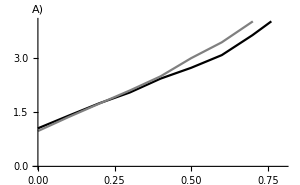
-Graphics-Coefficient of variationAutocorrelation (ρ)

```mathematica
f6a = Labeled[ListPlot[{mD, mI(*, maxD, minD,maxI,minI*)},PlotRange->{All,{0,4.}},Joined->True,PlotRangePadding->None,PlotStyle->{Black,Gray},AxesStyle->as,ImageSize-> is,AxesLabel->aA],{"Coefficient of variation","Autocorrelation (ρ)"},{Left, Bottom},RotateLabel->True,LabelStyle->ls]
```

### Change in dispersal

```mathematica
DAT = {};
Do[ (* for each value of f *)
 β = 20.; μ = 0.8;  s =0.3;
SP  = {{β,μ,s},{β,μ,s},{β,μ,s}};

 TT = 1170;

out =LotteryBoundary[ TT,ff ,σ= 0.8,Subscript[σ, l]=0.8, ρ =0., SP,seed = sed];

nout = out[[1,1;;-1;;10,1;;32;;4,1;;16;;4]];

dim = Dimensions[nout];
nout = Partition[Flatten[nout],dim[[2]]dim[[3]]]//Transpose;

FF =Round[ff 20,1];(*Print@FF;*)
(*AppendTo[DAT,nout];*)

name = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_f_"<>ToString[FF]<>"_seed_"<>ToString@sed<>".csv";
Export[ name,nout];
,{ff,Range[0.,0.5,0.05]},{sed,1,100,1}];
```

```mathematica
TIME= Range[11700, 200, -100];
finalI = finalD = {};
Do[
ICV = DCV = {};
Do[

namep = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_pp_f_"<>ToString[i]<>"_seed_"<>ToString@sed<>".csv";
namem = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_pm_f_"<>ToString[i]<>"_seed_"<>ToString@sed<>".csv";
dp = Import[namep][[2;;,;;-2]];
dm = Import[namem][[2;;,;;-2]];

IAC= DAC = {};
Do[
rTIME= TIME + RandomReal[{-50,50},Length@TIME];
Assert[Length@rTIME == Length@dp[[j]]];
ac = SeparateAC[{rTIME,dp[[j]],dm[[j]]},0.5,False];
iac = Select[ac,(#[[2]] ==-1)&];
dac = Select[ac,(#[[2]] ==1)&];
AppendTo[IAC, iac];
AppendTo[DAC, dac];
,{j, Length@dp}];

IAC = Partition[IAC//Flatten,2][[All,1]]//Sort;
dI = Differences@IAC;

DAC = Partition[DAC//Flatten,2][[All,1]]//Sort;
dD = Differences@DAC;

(* compute CV*)
iCV = StandardDeviation@dI/ Mean@dI//N;
dCV = StandardDeviation@dD/ Mean@dD//N;

AppendTo[ICV , iCV];
AppendTo[DCV , dCV];
,{i,0,10,1}];
AppendTo[finalI, ICV];
AppendTo[finalD,DCV];

,{sed, 100}];
```

```mathematica
mI ={Range[0,0.5,0.05],Mean@finalI}//Transpose;

(*maxI = {Range[0,0.5,0.05],Map[Max,Transpose@finalI]}//Transpose;
minI = {Range[0,0.5,0.05],Map[Min,Transpose@finalI]}//Transpose;*)

mD ={Range[0,0.5,0.05],Mean@finalD}//Transpose;
(*
maxD = {Range[0,0.5,0.05],Map[Max,Transpose@finalD]}//Transpose;
minD = {Range[0,0.5,0.05],Map[Min,Transpose@finalD]}//Transpose;
*)
```

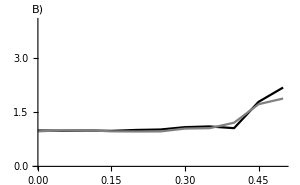
-Graphics-Coefficient of variationDispersal (f)

```mathematica
f6b = Labeled[ListPlot[{mD,mI(*, maxD, minD,maxI,minI*)},PlotRange->{All,{0,4}},Joined->True,LabelStyle->ls,PlotRangePadding->None,PlotStyle->{Black,Gray},AxesStyle->as,ImageSize-> is, AxesLabel->aB],{"Coefficient of variation","Dispersal (f)"},{Left, Bottom},RotateLabel->True,LabelStyle->ls]
```

```mathematica
lg6 = LineLegend[{Black, Gray},{"Abrupt decreases", "Abrupt increases"}]
```

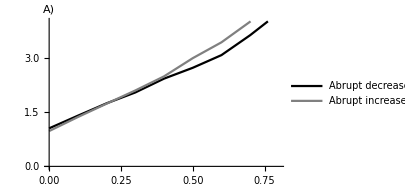
-Graphics-Coefficient of variationAutocorrelation (ρ) | -Graphics-Coefficient of variationDispersal (f)

```mathematica
F6 = Legended[Grid[{{f6a,f6b}},Spacings->{2, 1}],lg6]
```

```mathematica
Export["/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig6.pdf",F6]
```

/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig5.pdf

## Supplementary figures

### Appendix S1: Figure S1

```mathematica
ALLFIG = {};
Do[
(* import empirical data *)
DDA = {};
sID = Select[spID, #[[1]] ==spp&][[All,2]];
Do[ (* for each site *)
ed = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_"<>ToString@id<>".csv"];
AppendTo[DDA,ed];
,{id,sID}];

nn = Length@sID;
eg =  Text[Framed[Style["N = "<> ToString@nn,12,FontFamily->"Helevetica"],Background->White],Scaled[{0.85,.88}]];
lb = {"Relative abundance", "Years Before Present"}; 
f5=Labeled[ListLinePlot[DDA,Epilog->eg,PlotRange->pr3a,AxesOrigin->{8500,0},PlotStyle->Directive[Gray,AbsoluteThickness[0.6]],AxesStyle->as,PlotRangePadding->None,ImageSize->is ,ScalingFunctions->sf,LabelStyle->ls, PlotLabel->Style[spp,16,Italic,FontFamily->"Helvetica"],ImagePadding->ip],lb,{Left,Bottom},RotateLabel->True,LabelStyle->ls];

(* separates the abrupt increase and decrease from the empirical data *)
empi = DS[spp,All,"AI"]//DeleteMissing//Normal //Values//Flatten;
empd = DS[spp,All,"AD"]//DeleteMissing//Normal //Values//Flatten;

gd  = {empd,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[empd]]}//Transpose;
gi  = {empi,ConstantArray[Directive[Gray,AbsoluteThickness[1],Opacity[1]],Length[empi]]}//Transpose;

(* compute the coefficient of variation *)
edi = Differences[Sort@empi] ;
edd = Differences[Sort@empd] ;
If[Length@edi>2,
cvi1 = StandardDeviation@edi/Mean@edi,
"NA"
];
 
If[Length@edd>2,
cvd1 = StandardDeviation@edd/Mean@edd,
"NA"];

(* if there are not many sites, just plot the bars without the smoothing, might change the length to 3 or 4 *)
lb2 = {"Density", "Years Before Present"};
(* for abrupt decreases *)
If[Length@empd > 2,
eg =  Text[Framed[Style["N = "<> ToString@Length@empd<>"\nCV="<>ToString@Round[cvd1,0.02],12,FontFamily->"Helvetica"],Background->White],Scaled[{0.85,.88}]];
f5C= SmoothHistogram[empd,{200,"Gaussian"},
Epilog->eg,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.0017}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gd,None},LabelStyle->ls,PlotLabel->"Abrupt decreases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2],
eg = Text[Framed[Style["N = "<> ToString@Length@empd<>"\nCV= NA",12,FontFamily->"Helvetica"],Background->White],Scaled[{0.85,0.88}]];
f5C = ListLinePlot[{empd,1}//Flatten,Epilog->eg,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],PlotRange-> {{800,8500},{0,0.0017}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gd,None},LabelStyle->ls,PlotLabel->"Abrupt decreases",ImageSize->is,Ticks->tx,ImagePadding->ip2]
];
f5C = Labeled[f5C, lb2,{Left,Bottom},RotateLabel->True,LabelStyle->ls];

(* for abrupt increases *)
If[Length@empi >2,
eg = Text[Framed[Style["N = "<> ToString@Length@empi<>"\nCV="<>ToString@Round[cvi1,0.02],12,FontFamily->"Helvetica"],Background->White],Scaled[{0.85,.88}]];
f5E = SmoothHistogram[empi,{200,"Gaussian"},
Epilog->eg,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.0017}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gi,None},LabelStyle->ls,PlotLabel-> "Abrupt increases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2],
eg = Text[Framed[Style["N = "<> ToString@Length@empi<>"\nCV= NA",12,FontFamily->"Helvetica"],Background->White],Scaled[{0.85,.88}]];
f5E = ListLinePlot[{empi,1}//Flatten,Epilog->eg, AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],PlotRange-> {{800,8500},{0,0.0017}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gi,None},LabelStyle->ls,PlotLabel->"Abrupt increases",ImageSize->is,Ticks->tx,ImagePadding->ip2]
];
f5E= Labeled[f5E, lb2,{Left,Bottom},RotateLabel->True,LabelStyle->ls];

FF = {f5,f5C,f5E};
AppendTo[ALLFIG, FF];
,{spp, SP}];
```

```mathematica
sF1 = Grid[ALLFIG,Spacings->{Automatic, 2}];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/figS1.pdf",sF1]
```

### Appendix S1: Figure S2

#### Abrupt increase

```mathematica
(*pt1 = Graphics[{EdgeForm[{AbsoluteThickness[1], Gray}],FaceForm[None],Disk[{0,0},0.1]}];*)
pt2 = Graphics[{EdgeForm[{AbsoluteThickness[0.5], White}],FaceForm[ GrayLevel[(8000-#)/8000],Opacity[0.9]],Disk[{0,0},0.1]}]&;
pt1 = Graphics[Inset[Style["×",16,Orange]],ImageSize->15];
tl = Style[#,15, FontFamily->"Helvetica"]&/@Subdivide[8000,1000,5];
lg = BarLegend[GrayLevel, "TickLabels"->tl,LegendLabel-> Style["YBP       ",15,FontFamily->"Helvetica"]];
gr ={{37.,56.},{-105.,-59.}};
```

```mathematica
FIGI = {};
Do[

SeedRandom[1];
sda = DA[Select[#[sp] ==1 &],{"datasetID","lat","lon"}];

allp = {};
Do[
coord= sda[i,{"lat","lon"}]//Normal//Values;

siteID = sda[i,"datasetID"];
timeAC = DS[sp,siteID,"AI"];

 If[MissingQ[timeAC]==True,
gm = {GeoMarker[ RandomReal[{-0.35,0.35},2] +coord,pt1 ,"Scale"->1]};
AppendTo[allp,gm],

Do[
mark = pt2[timeAC[[j]]];
gm = {GeoMarker[ RandomReal[{-0.35,0.35},2] +coord,mark ,"Scale"->2]};
AppendTo[allp,gm];
,{j,Length@timeAC}];
];
,{i,Length@sda}];

pl = Row[{Style[sp,Italic , 20,FontFamily->"Helvetica"], Style[" abrupt increases",20,FontFamily->"Helvetica"]}];

ffA=Legended[GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,LabelStyle->ls ,PlotLabel-> pl] ,lg] ;
AppendTo[FIGI,ffA];
,{sp,SP}];
```

#### Abrupt decrease, export AI and AD

```mathematica
FIGD = {};
Do[

SeedRandom[1];
sda = DA[Select[#[sp] ==1 &],{"datasetID","lat","lon"}];

allp = {};
Do[
coord= sda[i,{"lat","lon"}]//Normal//Values;

siteID = sda[i,"datasetID"];
timeAC = DS[sp,siteID,"AD"];

 If[MissingQ[timeAC]==True,
gm = {GeoMarker[ RandomReal[{-0.35,0.35},2] +coord,pt1 ,"Scale"->1]};
AppendTo[allp,gm],

Do[
mark = pt2[timeAC[[j]]];
gm = {GeoMarker[ RandomReal[{-0.35,0.35},2] +coord,mark ,"Scale"->2]};
AppendTo[allp,gm];
,{j,Length@timeAC}];
];
,{i,Length@sda}];

(*allp = Table[{GeoMarker[ RandomReal[{-0.25,0.25},2] +,If[sda[i,sp<>"_AC"]==0,pt[[1]],pt[[2]]],"Scale"->sda[i,sp<>"_AC"]/10+0.8]},{i,Length@sda}];
*)

pl = Row[{Style[sp,Italic , 20,FontFamily->"Helvetica"], Style[" abrupt decreases",20,FontFamily->"Helvetica"]}];

ffA=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,LabelStyle->ls ,PlotLabel->pl];
AppendTo[FIGD,ffA];
,{sp,SP}];
```

```mathematica
FIGS2= Grid[Partition[Riffle[FIGD,FIGI],4],Spacings ->{{0,0,5,0,0,0},3}];

Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/figS2.pdf", FIGS2]
```

/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/figS2.pdf

### Appendix S2: Figure S1

```mathematica
lgS = PointLegend[{Gray,Black,Gray},{"Original data","Fitted with bcp","Abrupt changes"},LegendMarkers->{{Graphics[{Black,AbsoluteThickness[0.5],Line[{{1,0},{20,0}}]}],20},{"—",20},{"|",20}},LabelStyle->ls]
```

```mathematica
(* import data for all empirical data (time-series, fitted mean, and posterior probability *)
ED = EP = EM ={};
Do[
ed = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_"<>ToString@id<>".csv"][[2;;]];
em = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pm_"<>ToString@id<>".csv"][[2;;]];
ep = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pp_"<>ToString@id<>".csv"][[2;;]];

ep = Select[ep,(#[[2]] > 0.5)&];
AppendTo[ED,ed];
AppendTo[EM,em];
AppendTo[EP,ep];
,{id,finalID}];
```

```mathematica
(* plot all the panels *)
FIG = {};
Do[
gd = {Table[{EP[[i,j,1]],Directive[AbsoluteThickness[2],Opacity[1]]},{j,Length@EP[[i]]}],None};
fig = ListLinePlot[{ED[[i]],EM[[i]]},PlotRange->{All,{0,0.5}}, PlotStyle-> {{Black,Thin},Black},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{Max[ED[[i,All,1]]],0},GridLines->gd,FrameStyle->Directive[12,Black,FontFamily->"Arial"],
PlotRangePadding->None,Frame->True,PlotLabel->"Dataset ID: "<>ToString@ID[[i]], LabelStyle->Directive[12,Black,FontFamily->"Arial"],ImageSize->250];
AppendTo[FIG,fig];
,{i,Length@EP}];
PrependTo[FIG,lgS];
```

```mathematica
FF = Partition[FIG,4];
out =Labeled[Grid[FF],{"Years Before Present","Frequency","Figure S1"},{Bottom,Left,Top},RotateLabel->True,LabelStyle->Directive[16,Black,FontFamily->"Arial"]];
```

```mathematica
Export["/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/figS3.pdf",out]
```

/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/figS1.pdf